```mathematica
Quit[]
```

# fDES

### Packages Definitions

```mathematica
<<MaTeX` (* Package to plot with LaTeX format *)
Block[{Print},<<xAct`xPand`]; (* Package to compute cosmological perturbations *)
$DefInfoQ=False; (* No verbose *)
```

```mathematica
DefManifold[M,4,{α,β,γ,η,κ,λ,μ,ν,σ,τ}]
DefMetric[-1,g[-μ,-ν],CD,{";","∇"},PrintAs->"g"]
Block[{Print},SetSlicing[g,n,h,cd,{"|","∂"},"FLFlat"]]; (* Flat FLRW *)
DefMetricFields[g,δg,h];
DefMatterFields[u,δu,h];
MyToxPand[expr_,gauge_,order_]:=ToxPand[expr,δg,u,δu,h, gauge,order]
org[expr_]:=NoScalar@Collect[ContractMetric[expr],$PerturbationParameter,ToCanonical]
Unprotect[IndexForm];
IndexForm[LI[x_]]:=ColorString[ToString[x],RGBColor[1,0,0]];
Protect[IndexForm];
PrintAs[ϕh]^="Φ"; (* Gravitational Potentials *)
PrintAs[ψh]^="Ψ";
PrintAs[Eth]^="h"; (* Tensor Modes *)
$ConformalTime=False; (* Cosmic Time *)
$FirstOrderVectorPerturbations=False; (* No Vector Perturbations *)
$FirstOrderTensorPerturbations=False; (* No Tensor Perturbations *)
```

### Notation

```mathematica
(* Split of perturbations *)
MyGauge={δg[LI[1],-μ_,-ν_]:>-2n[-μ]*n[-ν]*ψh[LI[1]]+2h[-μ,-ν]*ϕh[LI[1]]}
```

{δg | 1 |   |  
  | μ̲ | ν̲:>-2 n^- |  
μ n^- |  
ν Ψ | 1
 +2 h^- |   |  
μ | ν Φ | 1
 }

```mathematica
(* Notation for derivatives of f(R) *)
DefScalarFunction[FR,PrintAs->"F_R"];
DefScalarFunction[FRR,PrintAs->"F_RR"];

(* 1 order SR parameters for the potentials *)
DefTensor[εΨ[],M,PrintAs->"ε_Ψ"]
DefTensorPerturbation[δεΨ[LI[1]],εΨ[],M,PrintAs->"δε_Ψ"];
DefTensor[εΦ[],M,PrintAs->"ε_Φ"]
DefTensorPerturbation[δεΦ[LI[1]],εΦ[],M,PrintAs->"δε_Φ"];  

(* 2 order SR parameters for the potentials *)
DefTensor[χΨ[],M,PrintAs->"χ_Ψ"]
DefTensorPerturbation[δχΨ[LI[1]],χΨ[],M,PrintAs->"δχ_Ψ"];
DefTensor[χΦ[],M,PrintAs->"χ_Φ"]
DefTensorPerturbation[δχΦ[LI[1]],χΦ[],M,PrintAs->"δχ_Φ"];  

(* SR parameters for the Hubble parameter *)
DefTensor[ε[],M] (* 1 order *)
DefTensorPerturbation[δε[LI[1]],ε[],M,PrintAs->"δε"]; 
 DefTensor[δ[],M] (* 2 order *)
DefTensorPerturbation[δδ[LI[1]],δ[],M,PrintAs->"δδ"];
DefTensor[ξ[],M] (* 3 order *)
DefTensorPerturbation[δξ[LI[1]],ξ[],M,PrintAs->"δξ"]; 
DefTensor[χ[],M] (* 4 order *)
DefTensorPerturbation[δχ[LI[1]],χ[],M,PrintAs->"δχ"];

(* Just to make things more readable *)
(* 1 order perturbation coefficients are red *)
MakeBoxes[εΨ[],StandardForm]:=StyleBox[ToString[εΨ],FontColor->Red]
MakeBoxes[εΦ[],StandardForm]:=StyleBox[ToString[εΦ],FontColor->Red]
(* 2 order perturbation coefficients are blue *)
MakeBoxes[χΨ[],StandardForm]:=StyleBox[ToString[χΨ],FontColor->Blue]
MakeBoxes[χΦ[],StandardForm]:=StyleBox[ToString[χΦ],FontColor->Blue]

(* Background SR parameters *)
MakeBoxes[ε[],StandardForm]:=StyleBox[ToString[ε],FontColor->Orange]
MakeBoxes[δ[],StandardForm]:=StyleBox[ToString[δ],FontColor->Purple]
MakeBoxes[ξ[],StandardForm]:=StyleBox[ToString[ξ],FontColor->Pink]
MakeBoxes[χ[],StandardForm]:=StyleBox[ToString[χ],FontColor->Brown]

(* Matter sector *)
DefScalarFunction[ρm,PrintAs->"ρ_m"];
DefScalarFunction[δm,PrintAs->"δ_m"];
DefScalarFunction[Vm,PrintAs->"V_m"];
```

## Background

```mathematica
DefScalarFunction[HN,PrintAs->"H"];
DefScalarFunction[aN,PrintAs->"a"];
```

```mathematica
ρDE=-f/2+3 (H^)^2+3 F (H^)^2+3 F Ḣ-3 H^ F'; (* DE density *)
PDE=f/2-3 (H^)^2-3 F (H^)^2-2 Ḣ-F Ḣ+2 H^ F'+F'';(* DE pressure *)
```

```mathematica
(* In ⅇ-folds time -> dt = a*dη = dN/H ⇒ dN = (a*H)dη *)
ρDENe=ρDE/.Ḣ->HN[Ne]*HN'[Ne]/.Hh[]->HN[Ne]/.f->f[R]/.F'->HN[Ne]*FR*Ra'[Ne]/.F->f'[R]/.FR->f''[R]//Expand
PDENe=PDE/.Ḣ->HN[Ne]*HN'[Ne]/.Hh[]->HN[Ne]/.f->f[R]/.F''->HN[Ne]*HN'[Ne]*FR*Ra'[Ne]+HN[Ne]^2*FR*Ra''[Ne]+HN[Ne]^2*FRR*Ra'[Ne]^2/.F'->HN[Ne]*FR*Ra'[Ne]/.F->f'[R]/.FRR->f'''[R]/.FR->f''[R]//Expand
```

-f[R]/2+3 H[Ne]^2+3 H[Ne]^2 f'[R]+3 H[Ne] f'[R] H'[Ne]-3 H[Ne]^2 Ra'[Ne] f''[R]

f[R]/2-3 H[Ne]^2-3 H[Ne]^2 f'[R]-2 H[Ne] H'[Ne]-H[Ne] f'[R] H'[Ne]+2 H[Ne]^2 Ra'[Ne] f''[R]+H[Ne] H'[Ne] Ra'[Ne] f''[R]+H[Ne]^2 f''[R] Ra''[Ne]+H[Ne]^2 Ra'[Ne]^2 f^(3)[R]

```mathematica
aN[Ne_]:=Exp[Ne] (* Scale factor in terms of N *)
Ωm[Ne_]:=Ωm0 aN[Ne]^-3 (* Matter density parameter *)
HN[Ne_]:=H0 √(Ωm[Ne]+ΩΛ) (* Hubble parameter in N time *)
Ra[Ne_]:=6(2 HN[Ne]^2+HN[Ne]*HN'[Ne]) (* Ricci scalar *)
(* fDES -> See Eq. (69) in 1811.02469 *)
c0=1/12(√73-7);
f[R_]:=(R-2Λ)+α*H0^2((Λ/(R-3 Λ))^c0  Hypergeometric2F1[c0,3/2+c0,13/6+2c0,Λ/(R-3 Λ)])/.Λ->3*H0^2 ΩΛ;
```

```mathematica
(* The background matches ΛCDM *)
ρDES=ρDENe/.R->Ra[Ne]/.Ωm0->1-ΩΛ//FullSimplify
PDES=PDENe/.R->Ra[Ne]/.Ωm0->1-ΩΛ//FullSimplify
```

3 H0^2 ΩΛ

-3 H0^2 ΩΛ

```mathematica
(* Since the background is ΛCDM: *)
H0=1; (* Hubble parameter today *);
h=0.67810; (* Reduced Hubble parameter *)
ωb=0.02238280; (* Subscript[Ω, b] h^2 *)
ωCDM=0.1201075; (* Subscript[Ω, CDM] h^2 *)
ωm=ωCDM+ωb;
Ωm0=(ωb+ωCDM)/h^2; (* Matter Today *)
ΩΛ=1-Ωm0; (* Dark Energy Today *)
fR0[α_]:=f'[R]-1/.R->Ra[Ne]/.Ne->Log[1]
αDES=Solve[fR0[α]==-10^-4,α]⟦1,1,2⟧ (* Value of α from Subscript[f, R,0] = -10^-4 -> See comment after Eq. (70) in 1811.02469 *)
```

0.00107239

### Approximated Expressions

```mathematica
Series[Series[f'[R]/.R->Ra[Log[a]],{α,0,1}],{a,0,2}]//Normal;
Simplify[%,Assumptions->a>0]/.α->αDES//N
```

1.-0.000164529 a^3.386

```mathematica
0.00016452934638598856
```

0.000164529

```mathematica
(* This is the expression in the designer.f90 *)
1+gom*fR0*a^ndes/.gom->1.671088041570895/.fR0->-10^-4/.ndes->3.386000936329383
```

1-0.000167109 a^3.386

## Sub-Horizon Parameters

```mathematica
{H0,Ωm0,ΩΛ}=.;
```

```mathematica
εSHA[Ne_,k_]:=(ⅇ^Ne*HN[Ne])/k
```

```mathematica
(* In general δ is non-negligible*)
δSHA[Ne_,k_]:=D[εSHA[Nⅇ,k],Nⅇ]/εSHA[Nⅇ,k]/.Nⅇ->Ne//Simplify
```

```mathematica
δSHA[Log[a],k]
%/.ΩΛ->0 (* δ during matter domination *)
%%/.Ωm0->0 (* δ during DE domination *)
```

-(Ωm0-2 a^3 ΩΛ)/(2 (Ωm0+a^3 ΩΛ))

-1/2

1

```mathematica
(* In general -> ξ = 1 is non-negligible*)
ξSHA[Ne_,k_]:=D[HN[Nⅇ]*D[εSHA[Nⅇ,k],Nⅇ],Nⅇ]/(HN[Nⅇ]*εSHA[Nⅇ,k])/.Nⅇ->Ne//Simplify
```

```mathematica
ξSHA[Ne,k]
```

1

```mathematica
(* In general χ is non-negligible*)
χSHA[Ne_,k_]:=(HN[Nⅇ]*D[HN[Nⅇ]*D[HN[Nⅇ]*D[εSHA[Nⅇ,k],Nⅇ],Nⅇ],Nⅇ])/(HN[Nⅇ]^3*εSHA[Nⅇ,k])/.Nⅇ->Ne//Simplify
```

```mathematica
χSHA[Log[a],k]
%/.ΩΛ->0 (* χ during matter domination *)
%%/.Ωm0->0 (* χ during DE domination *)
```

(-7 Ωm0+2 a^3 ΩΛ)/(2 (Ωm0+a^3 ΩΛ))

-7/2

1

```mathematica
H0=1; (* Hubble parameter today *);
h=0.67810; (* Reduced Hubble parameter *)
ωb=0.02238280; (* Subscript[Ω, b] h^2 *)
ωCDM=0.1201075; (* Subscript[Ω, CDM] h^2 *)
ωm=ωCDM+ωb;
Ωm0=(ωb+ωCDM)/h^2; (* Matter Today *)
ΩΛ=1-Ωm0; (* Dark Energy Today *)
```

```mathematica
(* Usually ε enter in even powers -> ε^2 < 10^-3 for k > 180 H0 *)Manipulate[LogLogPlot[{εSHA[Log[a],k]^2,1,0.1,0.01,0.001}//Evaluate,{a,10^-2,1},PlotRange->All,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->12}],{k,1,600,20},FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"a","\\varepsilon^2"},RotateLabel->False]
```

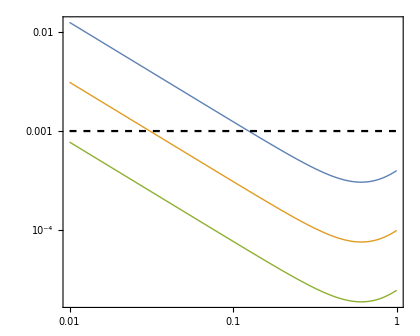

```mathematica
(* This is Fig.  in 2303. *)
LogLogPlot[{εSHA[Log[a],50H0]^2,εSHA[Log[a],100H0]^2,εSHA[Log[a],200H0]^2,0.001},{a,10^-2,1},PlotRange->{All,{0.1,10^-5}},PlotStyle->{Directive[Thick],Directive[Thick],Directive[Thick],Directive[Dashed,Black]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"a","\\varepsilon^2"},RotateLabel->False,BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.8,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["k = 50 H_0"],
(MaTeX[#,Magnification->1.2]&)/@Style["k = 100 H_0"],
(MaTeX[#,Magnification->1.2]&)/@Style["k = 200 H_0"]},
LegendLayout->{"Row",3},LegendMarkerSize->{35,15},LabelStyle->{Black,Bold,15},LegendFunction->Frame],
{0.8,0.78}],ImageSize->420]
```

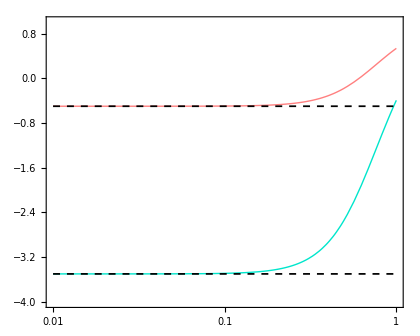

```mathematica
(* This is Fig.  in 2303. *)
LogLinearPlot[{δSHA[Log[a],k],χSHA[Log[a],k],-0.5,-3.5},{a,10^-2,1},PlotRange->{All,{-4,1}},PlotStyle->{Directive[Thick,RGBColor[1,0.5,0.5]],Directive[Thick,RGBColor[0.,0.9,0.8]],Directive[Dashed,Black,Thickness[0.003]],Directive[Dashed,Black,Thickness[0.003]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->14},AspectRatio->0.8,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.5]&)/@Style["\\delta"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\xi"]},
LegendLayout->{"Row",2},LegendMarkerSize->{40,15},LabelStyle->{Black,Bold}],
{0.2,0.4}],ImageSize->420]
```

## Perturbations

### Standard QSA and SHA

#### Expressions

```mathematica
Φstd[Ne_]:=(2 Subscript[F, R] k^2 (a^)^2+F (a^)^4)/(6 F Subscript[F, R] k^4+2 F^2 k^2 (a^)^2)/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
Ψstd[Ne_]:=-(4 Subscript[F, R] k^2 (a^)^2+F (a^)^4)/(6 F Subscript[F, R] k^4+2 F^2 k^2 (a^)^2)/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
δρDEstd[Ne_]:=-((-2+3 F) Subscript[F, R] k^2+(-1+F) F (a^)^2)/(F (3 Subscript[F, R] k^2+F (a^)^2))/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
δPDEstd[Ne_]:=(2 Subscript[F, R] k^4+15 Subscript[F, R] k^2 (a^)^2 F''+3 F (a^)^4 F'')/(9 F Subscript[F, R] k^4+3 F^2 k^2 (a^)^2)/.ah[]->aN[Ne]/.F''->HN[Ne]*HN'[Ne]*FR*Ra'[Ne]+HN[Ne]^2*FR*Ra''[Ne]+HN[Ne]^2*FRR*Ra'[Ne]^2/.F->f'[R]/.FRR->f'''[R]/.FR->f''[R]/.R->Ra[Ne]
VDEstd[Ne_]:=(a^ (6 Subscript[F, R] k^2+F (a^)^2) F')/(2 F (3 Subscript[F, R] k^2+F (a^)^2))/.ah[]->aN[Ne]/.F'->HN[Ne]*FR*Ra'[Ne]/.F->f'[R]/.FR->f''[R]/.R->Ra[Ne]
πDEstd[Ne_]:=1/F*(k^2/a^2*FR/F)/(1+3 k^2/a^2*FR/F)/.a->aN[Ne]/.F->f'[R]/.FR->f''[R]/.R->Ra[Ne]
```

```mathematica
(* Initial conditions *)
δ0=1; (* Overall Scale *)
ai=10^-3;(* Initial scale factor *)
δmi=δ0*ai(1+3*(HN[Log[ai]]^2*ai^2)/k^2);
Vmi=-δ0*H0*√Ωm0*ai^(1/2);
Φistd=Φstd[Log[a]]*3 H0^2 Ωm[Log[a]]*δmi/.α->αDES/.k->300H0/.a->ai//Quiet;
Ψistd=Ψstd[Log[a]]*3 H0^2 Ωm[Log[a]]*δmi/.α->αDES/.k->300H0/.a->ai//Quiet;

(* Evolution Equations Matter *)
Eqδm[a_]:=-δm'[a]-Vm[a]/(a^2*HN[Log[a]])-3D[Φstd[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a],a];
EqVm[a_]:=-Vm'[a]-Vm[a]/a+k^2/(a^2*HN[Log[a]])Ψstd[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a];
```

```mathematica
SolPertsstd=NDSolve[{Eqδm[a]==0,EqVm[a]==0,
δm[ai]==δmi,Vm[ai]==Vmi}/.α->αDES/.k->300H0,{δm,Vm},{a,ai,1},MaxStepSize->10^-4,MaxStepFraction->10^-4,StartingStepSize->10^-4,PrecisionGoal->11,AccuracyGoal->11,MaxSteps->20000000,InterpolationOrder->All,Method->{"EquationSimplification"->"Residual"}][[1]];
```

#### Results

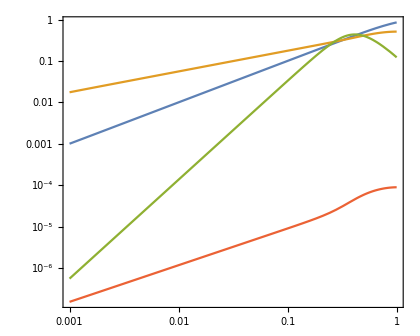

```mathematica
(* Perturbations *)
LogLogPlot[{δm[a],Vm[a],δρDEstd[Log[a]]*Ωm[Log[a]]/ΩΛ δm[a],VDEstd[Log[a]]*Ωm[Log[a]]/ΩΛ δm[a]}/.α->αDES/.k->300H0/.SolPertsstd//Abs//Evaluate,{a,ai,1},PlotRange->{3,10^-9},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.8,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["\\delta_m"],
(MaTeX[#,Magnification->1.3]&)/@Style["V_m"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\delta_\\text{DE}"],
(MaTeX[#,Magnification->1.3]&)/@Style["V_\\text{DE}"]},
LegendLayout->{"Row",4},LabelStyle->{Black,Bold,5},LegendFunction->Frame],
{0.885,0.23}],ImageSize->420]
```

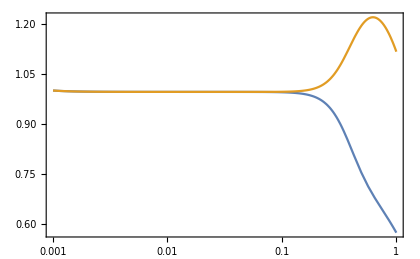

```mathematica
(* Potentials *)
LogLinearPlot[{(Φstd[Log[a]]*3 H0^2*Ωm[Log[a]]*δm[a])/(Φstd[Log[ai]]*3 H0^2*Ωm[Log[ai]]*δm[ai]),(Ψstd[Log[a]]*3 H0^2*Ωm[Log[a]]*δm[a])/(Ψstd[Log[ai]]*3 H0^2*Ωm[Log[ai]]*δm[ai])}/.α->αDES/.k->300H0/.SolPertsstd//Abs//Evaluate,{a,ai,1},Frame->True,PlotRange->All,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},PlotLegends->(MaTeX[#,Magnification->1.4]&)/@{"\\Phi/\\Phi_i","\\Psi/\\Psi_i"},BaseStyle->{FontFamily->"Times",FontSize->13},ImageSize->420]
```

```mathematica
(* Subscript[G, eff] -> grows at late times *)
Geffstd[a_]:=-2 k^2/a^2*Ψstd[Log[a]]/.α->αDES
```

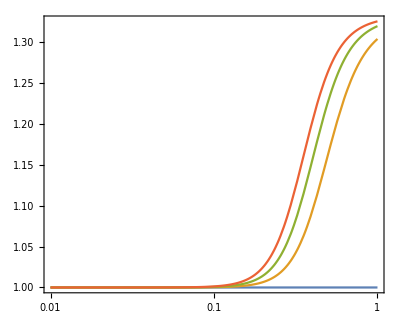

```mathematica
LogLinearPlot[{1,Geffstd[a]/.k->200,Geffstd[a]/.k->300,Geffstd[a]/.k->400}//Evaluate,{a,0.01,1},PlotRange->All,AspectRatio->0.8,Frame->True,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"a","\\frac{G_\\text{eff}}{G_N}"},RotateLabel->False,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

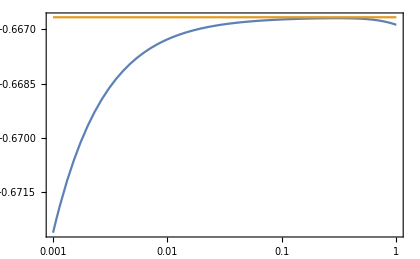

```mathematica
(* Sound Speed *)
LogLinearPlot[{δPDEstd[Log[a]]/δρDEstd[Log[a]],-2/3}/.α->αDES/.k->300H0/.SolPertsstd//Evaluate,{a,ai,1},PlotRange->All,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"a","c_s^2"},BaseStyle->{FontFamily->"Times",FontSize->13},RotateLabel->False,ImageSize->420]
```

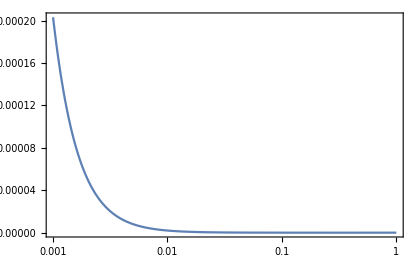

```mathematica
(* Effective Sound Speed *)
LogLinearPlot[{δPDEstd[Log[a]]/δρDEstd[Log[a]]-2/3*πDEstd[Log[a]]/δρDEstd[Log[a]]}/.α->αDES/.k->300H0//Evaluate,{a,ai,1},PlotRange->Full,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"a","c_\\text{eff}^2"},BaseStyle->{FontFamily->"Times",FontSize->13},RotateLabel->False,ImageSize->420]
```

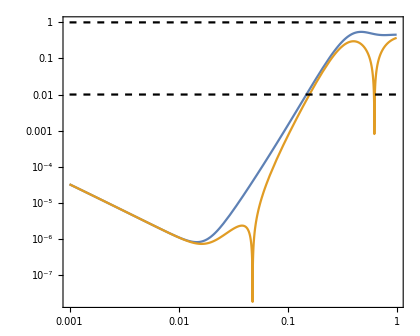

```mathematica
(* Check the consistency of QSA *)
LogLogPlot[{D[Φstd[Log[b]]*3 H0^2 Ωm[Log[b]]*δm[b],b]/(Φstd[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a]*a*HN[Log[a]]^2),D[Ψstd[Log[b]]*3 H0^2 Ωm[Log[b]]*δm[b],b]/(Ψstd[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a]*a*HN[Log[a]]^2),0.01,1}/.b->a/.α->αDES/.k->300H0/.SolPertsstd//Abs//Evaluate,{a,ai,1},PlotRange->All,PlotStyle->{"","",Directive[Black,Dashed],Directive[Black,Dashed]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.8,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["|\\varepsilon_\\Phi|"],
(MaTeX[#,Magnification->1.3]&)/@Style["|\\varepsilon_\\Psi|"]},
LegendLayout->{"Row",2},LabelStyle->{Black,Bold,15},LegendFunction->Frame],
{0.85,0.2}],ImageSize->420]
```

#### Expressions for CLASS

```mathematica
(* Approximations Subscript[for, 2] Subscript[F, 1] *)
Hyperf1=Series[Hypergeometric2F1[1/12 (-7+√73),1/12 (11+√73),1/6 (6+√73),(1. a^3)/(0.4490297476775782+1. a^3)],{a,0,20}]//Normal//CForm
```

1 + 0.19252696018912194*Power(a,3) - 0.24300138221994116*Power(a,6) + 0.3682433982846125*Power(a,9) - 
   0.6132729625153175*Power(a,12) + 1.0818858636459465*Power(a,15) - 1.9839657326851388*Power(a,18)

```mathematica
Hyperf2=Series[Hypergeometric2F1[1/12 (5+√73),1/12 (23+√73),2+(√73)/6,(1. a^3)/(0.4490297476775782+1. a^3)],{a,0,20}]//Normal//CForm
```

1 + 1.9297117448483008*Power(a,3) - 0.5458239036105854*Power(a,6) + 0.2962323094251147*Power(a,9) - 
   0.1958167348513662*Power(a,12) + 0.12268956323050872*Power(a,15) - 0.02894908612339009*Power(a,18)

```mathematica
Hyperf3=Series[ Hypergeometric2F1[1/12 (17+√73),1/12 (35+√73),3+(√73)/6,(1. a^3)/(0.4490297476775782+1. a^3)],{a,0,20}]//Normal//CForm
```

1 + 3.8883427731842883*Power(a,3) + 2.900491483532784*Power(a,6) - 1.1603513582705496*Power(a,9) + 
   0.7940835360072427*Power(a,12) - 0.6871944506934824*Power(a,15) + 0.6841986007669902*Power(a,18)

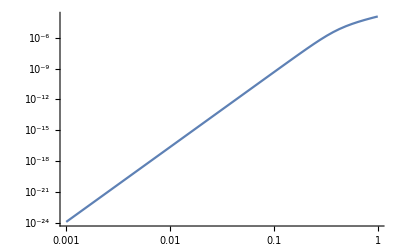

```mathematica
(* Validate approximated expression for Subscript[V, DE] *)
Series[VDEstd[Log[a]],{α,0,1}]//Normal//Simplify;
LogLogPlot[{%-VDEstd[Log[a]]}/.α->αDES/.k->300//Evaluate,{a,10^-3,1}]
```

```mathematica
αDES//CForm
```

0.00107239461666447

```mathematica
Series[VDEstd[Log[a]],{α,0,1}]//Normal//Simplify
```

-1/((0.44903+1. a^3)^3)0.0472449 √(0.690117+0.309883/a^3) a (a^3/(0.44903+1. a^3))^(1/12 (5+√73)) α ((0.201628+0.898059 a^3+1. a^6) Hypergeometric2F1[1/12 (-7+√73),1/12 (11+√73),1/6 (6+√73),(1. a^3)/(0.44903+1. a^3)]+(0.603399 a^3+1.34378 a^6) Hypergeometric2F1[1/12 (5+√73),1/12 (23+√73),2+(√73)/6,(1. a^3)/(0.44903+1. a^3)]+0.515824 a^6 Hypergeometric2F1[1/12 (17+√73),1/12 (35+√73),3+(√73)/6,(1. a^3)/(0.44903+1. a^3)])

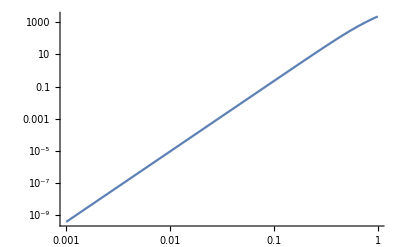

```mathematica
(* Validate approximated expression for Subscript[π, DE] -> Not a good approximation *)
Series[πDEstd[Log[a]],{α,0,1}]//Normal//Simplify;
LogLogPlot[{(%-πDEstd[Log[a]])/πDEstd[Log[a]]*100}/.α->αDES/.k->300//Evaluate,{a,10^-3,1}]
```

```mathematica
Series[πDEstd[Log[a]],{α,0,1}]//Normal//Simplify
%//CForm
```

1/((0.44903+1. a^3)^3)0.0338801 a (a^3/(0.44903+1. a^3))^(1/12 (5+√73)) k^2 α ((0.201628+0.898059 a^3+1. a^6) Hypergeometric2F1[1/12 (-7+√73),1/12 (11+√73),1/6 (6+√73),(1. a^3)/(0.44903+1. a^3)]+(0.603399 a^3+1.34378 a^6) Hypergeometric2F1[1/12 (5+√73),1/12 (23+√73),2+(√73)/6,(1. a^3)/(0.44903+1. a^3)]+0.515824 a^6 Hypergeometric2F1[1/12 (17+√73),1/12 (35+√73),3+(√73)/6,(1. a^3)/(0.44903+1. a^3)])

(0.033880125926161415*a*Power(Power(a,3)/(0.4490297476775782 + 1.*Power(a,3)),(5 + Sqrt(73))/12.)*
     Power(k,2)*α*((0.20162771429938953 + 0.8980594953551564*Power(a,3) + 1.*Power(a,6))*
        Hypergeometric2F1((-7 + Sqrt(73))/12.,(11 + Sqrt(73))/12.,(6 + Sqrt(73))/6.,
         (1.*Power(a,3))/(0.4490297476775782 + 1.*Power(a,3))) + 
       (0.6033991206303815*Power(a,3) + 1.3437842899077743*Power(a,6))*
        Hypergeometric2F1((5 + Sqrt(73))/12.,(23 + Sqrt(73))/12.,2 + Sqrt(73)/6.,
         (1.*Power(a,3))/(0.4490297476775782 + 1.*Power(a,3))) + 
       0.5158237069954171*Power(a,6)*Hypergeometric2F1((17 + Sqrt(73))/12.,(35 + Sqrt(73))/12.,
         3 + Sqrt(73)/6.,(1.*Power(a,3))/(0.4490297476775782 + 1.*Power(a,3)))))/
   Power(0.4490297476775782 + 1.*Power(a,3),3)

### 0^th Order in QSA

#### 0^th Order in SHA

```mathematica
(* Don't forget the factors Subscript[ρ̄, m] Subscript[δ, m] for the potentials and Subscript[ρ̄, m]/Subscript[ρ̄, DE] Subscript[δ, m] for the other perturbations *)
ΦQSASHA0[Ne_]:=(2 Subscript[F, R] k^2 (a^)^2+F (a^)^4)/(6 F Subscript[F, R] k^4+2 F^2 k^2 (a^)^2)/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
ΨQSASHA0[Ne_]:=-(4 Subscript[F, R] k^2 (a^)^2+F (a^)^4)/(6 F Subscript[F, R] k^4+2 F^2 k^2 (a^)^2)/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
δρQSASHA0[Ne_]:=((2-3 F) Subscript[F, R] k^2-(-1+F) F (a^)^2)/(F (3 Subscript[F, R] k^2+F (a^)^2))/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
δPQSASHA0[Ne_]:=(2 Subscript[F, R] k^2)/(9 F Subscript[F, R] k^2+3 F^2 (a^)^2)/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
VQSASHA0[Ne_]:=0
cs2QSASHA0[Ne_]:=-(2 (Subscript[F, R] k^2))/(3 (-2+3 F) Subscript[F, R] k^2+3 (-1+F) F (a^)^2)/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.α->αDES
```

```mathematica
(* Initial conditions *)
δ0=1; (* Overall Scale *)
ai=10^-3;(* Initial scale factor [z = 68] *)
δmi=δ0*ai(1+3*(HN[Log[ai]]^2*ai^2)/k^2);
Vmi=-δ0*H0*√Ωm0*ai^(1/2);

(* Evolution Equations Matter *)
Eqδm[a_]:=-δm'[a]-Vm[a]/(a^2*HN[Log[a]])-3D[ΦQSASHA0[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a],a];
EqVm[a_]:=-Vm'[a]-Vm[a]/a+k^2/(a^2*HN[Log[a]])ΨQSASHA0[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a];
```

```mathematica
SolPertsQSASHA0=NDSolve[{Eqδm[a]==0,EqVm[a]==0,
δm[ai]==δmi,Vm[ai]==Vmi}/.α->αDES/.k->300H0,{δm,Vm},{a,ai,1},Method->{"EquationSimplification"->"Residual"}][[1]];
```

#### 2^nd Order in SHA

```mathematica
(* Don't forget the factors Subscript[ρ̄, m] Subscript[δ, m] for the potentials and Subscript[ρ̄, m]/Subscript[ρ̄, DE] Subscript[δ, m] for the other perturbations *)
ΦQSASHA2[Ne_]:=(2 Subscript[F, R] k^2 (a^)^2+F (a^)^4)/(6 F Subscript[F, R] k^4+2 F^2 k^2 (a^)^2)-(3 ((a^)^2 (F^2 (a^)^4+F Subscript[F, R] k^2 (a^)^2 (8+δ)+2 Subscript[F, R]^2 k^4 (8+3 δ))) ε^2)/(2 (F (3 Subscript[F, R] k^3+F k (a^)^2)^2))/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
ΨQSASHA2[Ne_]:=-(4 Subscript[F, R] k^2 (a^)^2+F (a^)^4)/(6 F Subscript[F, R] k^4+2 F^2 k^2 (a^)^2)+(3 (a^)^2 (4 Subscript[F, R] k^2+F (a^)^2) (F (a^)^2+Subscript[F, R] k^2 (2-3 δ)) ε^2)/(2 F (3 Subscript[F, R] k^3+F k (a^)^2)^2)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
δρQSASHA2[Ne_]:=((2-3 F) Subscript[F, R] k^2-(-1+F) F (a^)^2)/(F (3 Subscript[F, R] k^2+F (a^)^2))-(3 (Subscript[F, R] k^2 (F (a^)^2 (1+δ)+2 Subscript[F, R] k^2 (2+3 δ))) ε^2)/(F (3 Subscript[F, R] k^2+F (a^)^2)^2)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
δPQSASHA2[Ne_]:=(2 Subscript[F, R] k^2)/(9 F Subscript[F, R] k^2+3 F^2 (a^)^2)+(((-1+F) F^2 (a^)^4 (1+2 δ)+F Subscript[F, R] k^2 (a^)^2 (-5+5 F-10 δ+13 F δ)+Subscript[F, R]^2 k^4 (-4-6 δ+3 F (2+7 δ))) ε^2)/(F (3 Subscript[F, R] k^2+F (a^)^2)^2)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
VQSASHA2[Ne_]:=(((-4+3 F) Subscript[F, R] k^3+(-1+F) F k (a^)^2) ε)/(F (3 Subscript[F, R] k^2+F (a^)^2))/.ε->εSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
πQSASHA2[Ne_]:=(Subscript[F, R] k^2)/(3 F Subscript[F, R] k^2+F^2 (a^)^2)+(3 Subscript[F, R] k^2 (Subscript[F, R] k^2 (4+9 δ)+(F+2 F δ) (a^)^2) ε^2)/(F (3 Subscript[F, R] k^2+F (a^)^2)^2)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
cs2QSASHA2[Ne_]:=-(2 (Subscript[F, R] k^2))/(3 (-2+3 F) Subscript[F, R] k^2+3 (-1+F) F (a^)^2)-(F ((-1+F)^2 F (a^)^4 (1+2 δ)+Subscript[F, R]^2 k^4 (-8+6 F-20 δ+21 F δ)+(-1+F) Subscript[F, R] k^2 (a^)^2 (-4-8 δ+F (5+13 δ))) ε^2)/(((-2+3 F) Subscript[F, R] k^2+(-1+F) F (a^)^2)^2)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.α->αDES
cs2effQSASHA2[Ne_]:=((-((-1+F) F (a^)^2 (1+2 δ))+Subscript[F, R] k^2 (4+8 δ-F (2+7 δ))) ε^2)/((-2+3 F) Subscript[F, R] k^2+(-1+F) F (a^)^2)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.α->αDES
```

```mathematica
(* Initial conditions *)
δ0=1; (* Overall Scale *)
ai=10^-3;(* Initial scale factor *)
δmi=δ0*ai(1+3*(HN[Log[ai]]^2*ai^2)/k^2);
Vmi=-δ0*H0*√Ωm0*ai^(1/2);
ΦiQSASHA=ΦQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δmi/.α->αDES/.k->300/.a->ai//Quiet;
ΨiQSASHA=ΨQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δmi/.α->αDES/.k->300/.a->ai//Quiet;
(* Evolution Equations Matter *)
Eqδm[a_]:=-δm'[a]-Vm[a]/(a^2*HN[Log[a]])-3D[ΦQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a],a];
EqVm[a_]:=-Vm'[a]-Vm[a]/a+k^2/(a^2*HN[Log[a]])ΨQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a];
```

```mathematica
SolPertsQSASHA2=NDSolve[{Eqδm[a]==0,EqVm[a]==0,
δm[ai]==δmi,Vm[ai]==Vmi}/.α->αDES/.k->300H0,{δm,Vm},{a,ai,1},Method->{"EquationSimplification"->"Residual"}][[1]];
```

```mathematica
(* Expressions for CLASS *)
Simplify[Series[VQSASHA2[Log[a]],{α,0,1}]//N//Normal,Assumptions->a>0]
%//CForm
```

-1/(a (0.44903+1. a^3)^10.5147)0.141297 √(0.690117+0.309883/a^3) α ((0.439837 a^5.386 (0.44903+1. a^3)^9.386+0.23978 a^6.386 (0.44903+1. a^3)^8.386 k^2) Hypergeometric2F1[0.128667,1.62867,2.424,(1. a^3)/(0.44903+1. a^3)]+(0.295523 (0.44903 a+1. a^4)^8.386+0.322213 a^9.386 (0.44903+1. a^3)^7.386 k^2) Hypergeometric2F1[1.12867,2.62867,3.424,(1. a^3)/(0.44903+1. a^3)]+0.123684 a^12.386 (0.44903+1. a^3)^6.386 k^2 Hypergeometric2F1[2.12867,3.62867,4.424,(1. a^3)/(0.44903+1. a^3)])

(-0.1412965389846828*Sqrt(0.6901169569518795 + 0.3098830430481206/Power(a,3))*α*
     ((0.43983686397089206*Power(a,5.386000936329383)*
           Power(0.4490297476775782 + 1.*Power(a,3),9.386000936329381) + 
          0.23978029589128283*Power(a,6.386000936329382)*
           Power(0.4490297476775782 + 1.*Power(a,3),8.386000936329381)*Power(k,2))*
        Hypergeometric2F1(0.12866697877646086,1.628666978776461,2.4240006242195884,
         (1.*Power(a,3))/(0.4490297476775782 + 1.*Power(a,3))) + 
       (0.29552293396319385*Power(0.4490297476775782*a + 1.*Power(a,4),8.386000936329381) + 
          0.3222129946481435*Power(a,9.386000936329381)*
           Power(0.4490297476775782 + 1.*Power(a,3),7.386000936329382)*Power(k,2))*
        Hypergeometric2F1(1.128666978776461,2.6286669787764607,3.4240006242195884,
         (1.*Power(a,3))/(0.4490297476775782 + 1.*Power(a,3))) + 
       0.12368436109109951*Power(a,12.386000936329381)*
        Power(0.4490297476775782 + 1.*Power(a,3),6.386000936329382)*Power(k,2)*
        Hypergeometric2F1(2.1286669787764607,3.6286669787764607,4.424000624219588,
         (1.*Power(a,3))/(0.4490297476775782 + 1.*Power(a,3)))))/
   (a*Power(0.4490297476775782 + 1.*Power(a,3),10.514667915105843))

```mathematica
Simplify[Series[πQSASHA2[Log[a]],{α,0,1}]//N//Normal,Assumptions->a>0]
%//CForm
```

1/a^3 0.990518 α (((-7.86207×10^-18 a^6.386+0.212446 a^9.386+0.0342044 a^7.386 k^2) Hypergeometric2F1[0.128667,1.62867,2.424,(1. a^3)/(0.44903+1. a^3)])/((0.44903+1. a^3)^2.12867)+((-1.05649×10^-17 a^9.386+0.285481 a^12.386+0.0459634 a^10.386 k^2) Hypergeometric2F1[1.12867,2.62867,3.424,(1. a^3)/(0.44903+1. a^3)])/((0.44903+1. a^3)^3.12867)+((-4.05544×10^-18 a^12.386+0.109584 a^15.386+0.0176435 a^13.386 k^2) Hypergeometric2F1[2.12867,3.62867,4.424,(1. a^3)/(0.44903+1. a^3)])/((0.44903+1. a^3)^4.12867))

(0.9905184087539354*α*(((-7.862065319997261e-18*Power(a,6.386000936329382) + 
            0.212445566673013*Power(a,9.386000936329381) + 
            0.03420443843015735*Power(a,7.386000936329382)*Power(k,2))*
          Hypergeometric2F1(0.12866697877646086,1.628666978776461,2.4240006242195884,
           (1.*Power(a,3))/(0.4490297476775782 + 1.*Power(a,3))))/
        Power(0.4490297476775782 + 1.*Power(a,3),2.12866697877646) + 
       ((-1.056491986324106e-17*Power(a,9.386000936329381) + 
            0.28548101495574957*Power(a,12.386000936329381) + 
            0.04596338700756319*Power(a,10.386000936329381)*Power(k,2))*
          Hypergeometric2F1(1.128666978776461,2.6286669787764607,3.4240006242195884,
           (1.*Power(a,3))/(0.4490297476775782 + 1.*Power(a,3))))/
        Power(0.4490297476775782 + 1.*Power(a,3),3.12866697877646) + 
       ((-4.055439678001098e-18*Power(a,12.386000936329381) + 
            0.10958445973601565*Power(a,15.386000936329381) + 
            0.017643460226740276*Power(a,13.386000936329381)*Power(k,2))*
          Hypergeometric2F1(2.1286669787764607,3.6286669787764607,4.424000624219588,
           (1.*Power(a,3))/(0.4490297476775782 + 1.*Power(a,3))))/
        Power(0.4490297476775782 + 1.*Power(a,3),4.12866697877646)))/Power(a,3)

#### 4^th Order in SHA

```mathematica
(* Don't forget the factors Subscript[ρ̄, m] Subscript[δ, m] for the potentials and Subscript[ρ̄, m]/Subscript[ρ̄, DE] Subscript[δ, m] for the other perturbations *)
ΦQSASHA4[Ne_]:=(2 Subscript[F, R] k^2 (a^)^2+F (a^)^4)/(6 F Subscript[F, R] k^4+2 F^2 k^2 (a^)^2)-(3 ((a^)^2 (F^2 (a^)^4+F Subscript[F, R] k^2 (a^)^2 (8+δ)+2 Subscript[F, R]^2 k^4 (8+3 δ))) ε^2)/(2 (F (3 Subscript[F, R] k^3+F k (a^)^2)^2))-1/(2 (F^2 k^2 (3 Subscript[F, R] k^2+F (a^)^2)^3))9 (-F^4 (a^)^8-2 F^3 Subscript[F, R] k^2 (a^)^6 (7-δ+δ^2-ξ)+60 Subscript[F, R]^4 k^8 (-2+δ+ξ)+F^2 Subscript[F, R]^2 k^4 (a^)^4 (-72+26 δ-7 δ^2+20 ξ)+2 F Subscript[F, R]^3 k^6 (a^)^2 (-78+43 δ+3 δ^2+31 ξ)) ε^4/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
ΨQSASHA4[Ne_]:=-(4 Subscript[F, R] k^2 (a^)^2+F (a^)^4)/(6 F Subscript[F, R] k^4+2 F^2 k^2 (a^)^2)+(3 (a^)^2 (4 Subscript[F, R] k^2+F (a^)^2) (F (a^)^2+Subscript[F, R] k^2 (2-3 δ)) ε^2)/(2 F (3 Subscript[F, R] k^3+F k (a^)^2)^2)+(9 (4 Subscript[F, R] k^2+F (a^)^2) (-F^3 (a^)^6+30 Subscript[F, R]^3 k^6 (-2+δ+ξ)+2 F^2 Subscript[F, R] k^2 (a^)^4 (-4+3 δ-δ^2+ξ)+F Subscript[F, R]^2 k^4 (a^)^2 (-36+22 δ-15 δ^2+16 ξ)) ε^4)/(2 F^2 k^2 (3 Subscript[F, R] k^2+F (a^)^2)^3)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
δρQSASHA4[Ne_]:=((2-3 F) Subscript[F, R] k^2-(-1+F) F (a^)^2)/(F (3 Subscript[F, R] k^2+F (a^)^2))-(3 (Subscript[F, R] k^2 (F (a^)^2 (1+δ)+2 Subscript[F, R] k^2 (2+3 δ))) ε^2)/(F (3 Subscript[F, R] k^2+F (a^)^2)^2)+(9 Subscript[F, R] k^2 (F^2 Subscript[F, R] k^2 (a^)^4 (46-5 δ+7 δ^2-20 ξ)+F^3 (a^)^6 (5+δ+2 δ^2-2 ξ)-60 Subscript[F, R]^3 k^6 (-2+δ+ξ)-2 F Subscript[F, R]^2 k^4 (a^)^2 (-66+25 δ+3 δ^2+31 ξ)) ε^4)/(F^2 (a^)^2 (3 Subscript[F, R] k^2+F (a^)^2)^3)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
δPQSASHA4[Ne_]:=(2 Subscript[F, R] k^2)/(9 F Subscript[F, R] k^2+3 F^2 (a^)^2)+(((-1+F) F^2 (a^)^4 (1+2 δ)+F Subscript[F, R] k^2 (a^)^2 (-5+5 F-10 δ+13 F δ)+Subscript[F, R]^2 k^4 (-4-6 δ+3 F (2+7 δ))) ε^2)/(F (3 Subscript[F, R] k^2+F (a^)^2)^2)+1/(F^2 (a^)^2 (3 Subscript[F, R] k^2+F (a^)^2)^3)3 (-((-1+F) F^4 (a^)^8 (1+2 δ))+30 Subscript[F, R]^4 k^8 (-2 (-2+δ+ξ)+3 F (2-6 δ+δ^2+2 ξ+χ))+F^3 Subscript[F, R] k^2 (a^)^6 (7+11 δ-6 δ^2+F (-7-32 δ+6 δ^2+4 ξ+2 χ))+F^2 Subscript[F, R]^2 k^4 (a^)^4 (22+11 δ-26 δ^2-4 ξ+F (4-200 δ+49 δ^2+44 ξ+22 χ))+F Subscript[F, R]^3 k^6 (a^)^2 (72-20 δ-6 δ^2-32 ξ+3 F (36-182 δ+41 δ^2+52 ξ+26 χ))) ε^4/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.χ->χSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
VQSASHA4[Ne_]:=(((-4+3 F) Subscript[F, R] k^3+(-1+F) F k (a^)^2) ε)/(F (3 Subscript[F, R] k^2+F (a^)^2))+(3 k (-((-1+F) F^2 (a^)^6)+18 Subscript[F, R]^3 k^6 (-2+δ+ξ)+F Subscript[F, R] k^2 (a^)^4 (6-3 δ+F (-9+2 δ+ξ))+Subscript[F, R]^2 k^4 (a^)^2 (8-12 δ+3 F (-10+4 δ+3 ξ))) ε^3)/(F (3 Subscript[F, R] k^2 a^+F (a^)^3)^2)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
cs2QSASHA4[Ne_]:=-(2 (Subscript[F, R] k^2))/(3 (-2+3 F) Subscript[F, R] k^2+3 (-1+F) F (a^)^2)-(F ((-1+F)^2 F (a^)^4 (1+2 δ)+Subscript[F, R]^2 k^4 (-8+6 F-20 δ+21 F δ)+(-1+F) Subscript[F, R] k^2 (a^)^2 (-4-8 δ+F (5+13 δ))) ε^2)/(((-2+3 F) Subscript[F, R] k^2+(-1+F) F (a^)^2)^2)-1/((a^)^2 ((-2+3 F) Subscript[F, R] k^2+(-1+F) F (a^)^2)^3)3 (-(-1+F)^3 F^3 (a^)^8 (1+2 δ)+10 (-2+3 F) Subscript[F, R]^4 k^8 (3 F (2-6 δ+δ^2+2 ξ+χ)-2 (-5 δ+δ^2+3 ξ+χ))+(-1+F)^2 F^2 Subscript[F, R] k^2 (a^)^6 (4+4 δ-8 δ^2+F (-7-32 δ+6 δ^2+4 ξ+2 χ))+(-1+F) F Subscript[F, R]^2 k^4 (a^)^4 (16 δ (1+2 δ)-2 F (-2-68 δ+41 δ^2+20 ξ+9 χ)+F^2 (4-200 δ+49 δ^2+44 ξ+22 χ))+F Subscript[F, R]^3 k^6 (a^)^2 (4 (6-65 δ+28 δ^2+31 ξ+12 χ)+3 F^2 (36-182 δ+41 δ^2+52 ξ+26 χ)-4 F (30-197 δ+58 δ^2+70 ξ+31 χ))) ε^4/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.χ->χSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.α->αDES
cs2effQSASHA4[Ne_]:=((-((-1+F) F (a^)^2 (1+2 δ))+Subscript[F, R] k^2 (4+8 δ-F (2+7 δ))) ε^2)/((-2+3 F) Subscript[F, R] k^2+(-1+F) F (a^)^2)+1/(((-2+3 F) Subscript[F, R] k^2 a^+(-1+F) F (a^)^3)^2)(3 (-1+F)^2 F^2 (a^)^6 (1+2 δ)-30 (-2+3 F) Subscript[F, R]^3 k^6 (2-6 δ+δ^2+2 ξ+χ)-6 (-1+F) F Subscript[F, R] k^2 (a^)^4 (2+2 δ-4 δ^2+F (-2-13 δ+3 δ^2+2 ξ+χ))-3 Subscript[F, R]^2 k^4 (a^)^2 (16 δ (1+2 δ)-2 F (6-46 δ+31 δ^2+14 ξ+7 χ)+F^2 (-122 δ+31 δ^2+16 (1+2 ξ+χ)))) ε^4/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.χ->χSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.α->αDES
```

```mathematica
(* Initial conditions *)
δ0=1; (* Overall Scale *)
ai=10^-3;(* Initial scale factor *)
δmi=δ0*ai(1+3*(HN[Log[ai]]^2*ai^2)/k^2);
Vmi=-δ0*H0*√Ωm0*ai^(1/2);

(* Evolution Equations Matter *)
Eqδm[a_]:=-δm'[a]-Vm[a]/(a^2*HN[Log[a]])-3D[ΦQSASHA4[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a],a];
EqVm[a_]:=-Vm'[a]-Vm[a]/a+k^2/(a^2*HN[Log[a]])ΨQSASHA4[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a];
```

```mathematica
SolPertsQSASHA4=NDSolve[{Eqδm[a]==0,EqVm[a]==0,
δm[ai]==δmi,Vm[ai]==Vmi}/.α->αDES/.k->300H0,{δm,Vm},{a,ai,1},Method->{"EquationSimplification"->"Residual"}][[1]];
```

#### Full in SHA

```mathematica
(* Don't forget the factors Subscript[ρ̄, m] Subscript[δ, m] for the potentials and Subscript[ρ̄, m]/Subscript[ρ̄, DE] Subscript[δ, m] for the other perturbations *)
ΦQSASHAFull[Ne_]:=((a^)^4 (F (a^)^2-2 Subscript[F, R] k^2 (-1+6 (1+δ) ε^2)))/(F^2 k^2 (a^)^4 (2+6 ε^2)-6 F Subscript[F, R] k^4 (a^)^2 (-1+(-2+3 δ) ε^2+6 ε^4 (2+δ^2-ξ))+36 Subscript[F, R]^2 k^6 ε^4 (5+6 (1+δ) ε^2) (-2+δ+ξ))/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
ΨQSASHAFull[Ne_]:=-((a^)^4 (4 Subscript[F, R] k^2+F (a^)^2))/(F^2 k^2 (a^)^4 (2+6 ε^2)-6 F Subscript[F, R] k^4 (a^)^2 (-1+(-2+3 δ) ε^2+6 ε^4 (2+δ^2-ξ))+36 Subscript[F, R]^2 k^6 ε^4 (5+6 (1+δ) ε^2) (-2+δ+ξ))/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
δρQSASHAFull[Ne_]:=-(((k^2 (F (a^)^2-2 Subscript[F, R] k^2 (-1+6 (1+δ) ε^2)) ((a^)^2 (-2+F+3 F δ ε^2)-18 Subscript[F, R] k^2 ε^4 (-2+δ+ξ))+(4 Subscript[F, R] k^2+F (a^)^2) (k^2 (a^)^2 (F-6 ε^2-3 F (-2+δ) ε^2)+54 Subscript[F, R] k^4 ε^4 (-2+δ+ξ))))/(F^2 k^2 (a^)^4 (2+6 ε^2)-6 F Subscript[F, R] k^4 (a^)^2 (-1+(-2+3 δ) ε^2+6 ε^4 (2+δ^2-ξ))+36 Subscript[F, R]^2 k^6 ε^4 (5+6 (1+δ) ε^2) (-2+δ+ξ)))/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
δPQSASHAFull[Ne_]:=((-((F (a^)^2-2 Subscript[F, R] k^2 (-1+6 (1+δ) ε^2)) (k^2 (a^)^4 (2-3 F (2+δ) ε^2)+108 Subscript[F, RR] k^6 ε^6 (-2+δ+ξ)^2+18 Subscript[F, R] k^4 (a^)^2 ε^4 (2-6 δ+δ^2+2 ξ+χ)))+(4 Subscript[F, R] k^2+F (a^)^2) (k^2 (a^)^4 (2+3 (-2+(-4+3 F) δ) ε^2)+324 Subscript[F, RR] k^6 ε^6 (-2+δ+ξ)^2+54 Subscript[F, R] k^4 (a^)^2 ε^4 (2-6 δ+δ^2+2 ξ+χ))))/(3 (a^)^2 (F^2 k^2 (a^)^4 (2+6 ε^2)-6 F Subscript[F, R] k^4 (a^)^2 (-1+(-2+3 δ) ε^2+6 ε^4 (2+δ^2-ξ))+36 Subscript[F, R]^2 k^6 ε^4 (5+6 (1+δ) ε^2) (-2+δ+ξ)))/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.χ->χSHA[Ne,k]/.ah[]->aN[Ne]/.FRR->f'''[R]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
VQSASHAFull[Ne_]:=(k^3 (4 Subscript[F, R] k^2+F (a^)^2) ε ((-2+F) (a^)^2+12 Subscript[F, R] k^2 ε^2 (-2+δ+ξ))+(F (a^)^2-2 Subscript[F, R] k^2 (-1+6 (1+δ) ε^2)) (F k^3 (a^)^2 ε-6 Subscript[F, R] k^5 ε^3 (-2+δ+ξ)))/(F^2 k^2 (a^)^4 (2+6 ε^2)-6 F Subscript[F, R] k^4 (a^)^2 (-1+(-2+3 δ) ε^2+6 ε^4 (2+δ^2-ξ))+36 Subscript[F, R]^2 k^6 ε^4 (5+6 (1+δ) ε^2) (-2+δ+ξ))/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
πQSASHAFull[Ne_]:=(2 Subscript[F, R] k^4(a^)^2 (1+6 (1+δ) ε^2))/(F^2 k^2 (a^)^4 (2+6 ε^2)-6 F Subscript[F, R] k^4 (a^)^2 (-1+(-2+3 δ) ε^2+6 ε^4 (2+δ^2-ξ))+36 Subscript[F, R]^2 k^6 ε^4 (5+6 (1+δ) ε^2) (-2+δ+ξ))/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
cs2QSASHAFull[Ne_]:=-((-((F (a^)^2-2 Subscript[F, R] k^2 (-1+6 (1+δ) ε^2)) (k^2 (a^)^4 (2-3 F (2+δ) ε^2)+108 Subscript[F, RR] k^6 ε^6 (-2+δ+ξ)^2+18 Subscript[F, R] k^4 (a^)^2 ε^4 (2-6 δ+δ^2+2 ξ+χ)))+(4 Subscript[F, R] k^2+F (a^)^2) (k^2 (a^)^4 (2+3 (-2+(-4+3 F) δ) ε^2)+324 Subscript[F, RR] k^6 ε^6 (-2+δ+ξ)^2+54 Subscript[F, R] k^4 (a^)^2 ε^4 (2-6 δ+δ^2+2 ξ+χ)))/(3 (a^)^2 (k^2 (F (a^)^2-2 Subscript[F, R] k^2 (-1+6 (1+δ) ε^2)) ((a^)^2 (-2+F+3 F δ ε^2)-18 Subscript[F, R] k^2 ε^4 (-2+δ+ξ))+(4 Subscript[F, R] k^2+F (a^)^2) (k^2 (a^)^2 (F-6 ε^2-3 F (-2+δ) ε^2)+54 Subscript[F, R] k^4 ε^4 (-2+δ+ξ)))))/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.χ->χSHA[Ne,k]/.ah[]->aN[Ne]/.FRR->f'''[R]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.α->αDES
cs2effQSASHAFull[Ne_]:=(4 Subscript[F, R] k^4 (a^)^4 (1+6 (1+δ) ε^2)+(F (a^)^2-2 Subscript[F, R] k^2 (-1+6 (1+δ) ε^2)) (k^2 (a^)^4 (2-3 F (2+δ) ε^2)+108 Subscript[F, RR] k^6 ε^6 (-2+δ+ξ)^2+18 Subscript[F, R] k^4 (a^)^2 ε^4 (2+(-6+δ) δ+2 ξ+χ))-(4 Subscript[F, R] k^2+F (a^)^2) (k^2 (a^)^4 (2+3 (-2+(-4+3 F) δ) ε^2)+324 Subscript[F, RR] k^6 ε^6 (-2+δ+ξ)^2+54 Subscript[F, R] k^4 (a^)^2 ε^4 (2+(-6+δ) δ+2 ξ+χ)))/(3 (a^)^2 (k^2 (F (a^)^2-2 Subscript[F, R] k^2 (-1+6 (1+δ) ε^2)) ((a^)^2 (-2+F+3 F δ ε^2)-18 Subscript[F, R] k^2 ε^4 (-2+δ+ξ))+(4 Subscript[F, R] k^2+F (a^)^2) (k^2 (a^)^2 (F-6 ε^2-3 F (-2+δ) ε^2)+54 Subscript[F, R] k^4 ε^4 (-2+δ+ξ))))/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ξ->ξSHA[Ne,k]/.χ->χSHA[Ne,k]/.ah[]->aN[Ne]/.FRR->f'''[R]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.α->αDES
```

```mathematica
(* Initial conditions *)
δ0=1; (* Overall Scale *)
ai=10^-3;(* Initial scale factor *)
δmi=δ0*ai(1+3*(HN[Log[ai]]^2*ai^2)/k^2);
Vmi=-δ0*H0*√Ωm0*ai^(1/2);

(* Evolution Equations Matter *)
Eqδm[a_]:=-δm'[a]-Vm[a]/(a^2*HN[Log[a]])-3D[ΦQSASHAFull[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a],a];
EqVm[a_]:=-Vm'[a]-Vm[a]/a+k^2/(a^2*HN[Log[a]])ΨQSASHAFull[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a];
```

```mathematica
SolPertsQSASHAFull=NDSolve[{Eqδm[a]==0,EqVm[a]==0,
δm[ai]==δmi,Vm[ai]==Vmi}/.α->αDES/.k->300H0,{δm,Vm},{a,ai,1},Method->{"EquationSimplification"->"Residual"}][[1]];
```

## Full Solution

### Fortran Data

```mathematica
DataFortran=Import["/Users/cosmologygroup/Desktop/QSA_Project/Theoretical_Work/Bayron/fDES_k_300.txt","Data"];
DataΔ=DataFortran[[All,{1,2}]];
Datav=DataFortran[[All,{1,3}]];
DataΦPlus=DataFortran[[All,{1,4}]];
Dataχ=DataFortran[[All,{1,5}]];
```

```mathematica
DataΦ=Table[{DataΦPlus[[i,1]],(-DataΦPlus[[i,2]]-Dataχ[[i,2]]/(2F))}/.F->f'[R]/.R->Ra[Ne]/.Ne->Log[DataΦPlus[[i,1]]]/.α->αDES//N,{i,1,Length[DataΦPlus]}];
DataΨ=Table[{DataΦPlus[[i,1]],(DataΦPlus[[i,2]]-Dataχ[[i,2]]/(2F))}/.F->f'[R]/.R->Ra[Ne]/.Ne->Log[DataΦPlus[[i,1]]]/.α->αDES//N,{i,1,Length[DataΦPlus]}];
```

### Potentials

```mathematica
ΦSR[a_]=ΦiQSASHA*FindFormula[DataΦ][a]//Expand
ΨSR[a_]=-ΨiQSASHA*FindFormula[DataΨ][a]//Expand
```

5.17544×10^-6-1.30042×10^-6 a+0.0000258107 a^2.-0.000170193 a^3.+0.000360699 a^4.-0.000321979 a^5.+0.000104771 a^5.99835

-5.14658×10^-6-1.6509×10^-6 a+0.0000300782 a^2-0.000184574 a^3+0.000387567 a^4-0.000341703 a^5+0.000109671 a^6

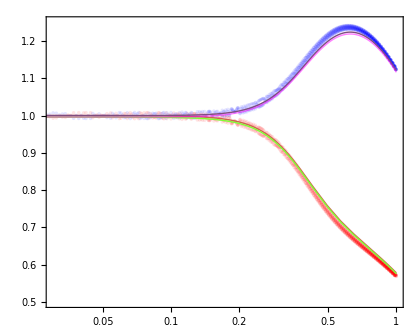

```mathematica
(* Comparison of the Potentials *)
ListLogLinearPlot[{DataΦ,DataΨ}//Abs,PlotRange->All,PlotStyle->{Directive[PointSize[0.006],Red,Opacity[0.1]],Directive[PointSize[0.006],Blue,Opacity[0.1]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},RotateLabel->False,BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["\\Phi^\\text{Full}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\Psi^\\text{Full}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,30},LegendMarkerSize->{25,25}],
{0.32,0.38}],ImageSize->420,AspectRatio->0.8];
LogLinearPlot[{(ΦQSASHA2[Log[a]]*3 H0^2*Ωm[Log[a]]*δm[a])/(ΦQSASHA2[Log[ai]]*3 H0^2*Ωm[Log[ai]]*δm[ai])/.SolPertsQSASHA2,(Φstd[Log[a]]*3 H0^2*Ωm[Log[a]]*δm[a])/(Φstd[Log[ai]]*3 H0^2*Ωm[Log[ai]]*δm[ai])/.SolPertsstd,(ΨQSASHA2[Log[a]]*3 H0^2*Ωm[Log[a]]*δm[a])/(ΨQSASHA2[Log[ai]]*3 H0^2*Ωm[Log[ai]]*δm[ai])/.SolPertsQSASHA2,(Ψstd[Log[a]]*3 H0^2*Ωm[Log[a]]*δm[a])/(Ψstd[Log[ai]]*3 H0^2*Ωm[Log[ai]]*δm[ai])/.SolPertsstd}/.α->αDES/.k->300H0//Abs//Evaluate,{a,ai,1},PlotRange->All,PlotStyle->{Directive[RGBColor[0.8,0.4,0.3],Thick],Directive[Thick,RGBColor[0.5,1,0.2]],Directive[RGBColor[0.5,0.3,0.5],Thick],Directive[Thick,Magenta,Opacity[0.5]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},RotateLabel->False,BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["\\Phi^\\text{SHA, 2}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\Phi^\\text{std}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\Psi^\\text{SHA, 2}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\Psi^\\text{std}"]},
LegendLayout->{"Row",2},LabelStyle->{Black,Bold,10},LegendMarkerSize->{35,15}],
{0.3,0.18}],ImageSize->420,AspectRatio->0.8];
Show[%%,%,PlotRange->{{Log[0.03],Log[1]},{0.5,1.25}},Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(\\emph{f}DES)}"],Scaled[{0.2,0.82}]]}]
```

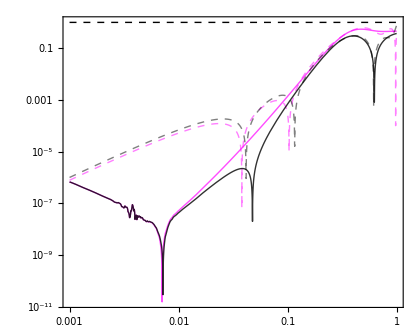

```mathematica
(* Comparison of the several ε parameters  *)
LogLogPlot[{D[ΦQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a],a]/(ΦQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a]*a*HN[Log[a]]^2)/.SolPertsQSASHA2,ΦSR'[a]/(ΦSR[a]*a*HN[Log[a]]^2),D[ΨQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a],a]/(ΨQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a]*a*HN[Log[a]]^2)/.SolPertsQSASHA2,ΨSR'[a]/(ΨSR[a]*a*HN[Log[a]]^2),1}/.α->αDES/.k->300//Abs//Evaluate,{a,ai,1},PlotRange->All,PlotStyle->{Directive[Thick,Magenta,Opacity[0.7]],Directive[Thick,Dashed,Magenta,Opacity[0.5]],Directive[Thick,Black,Opacity[0.8]],Directive[Thick,Black,Opacity[0.5],Dashed],Directive[Thick,Black,Dashed]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["\\varepsilon_\\Phi^\\text{SHA, 2}"],(MaTeX[#,Magnification->1.3]&)/@Style["\\varepsilon_\\Phi^\\text{Full}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\varepsilon_\\Psi^\\text{SHA, 2}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\varepsilon_\\Psi^\\text{Full}"]},
LegendLayout->{"Row",2},LabelStyle->{Black,Bold,15},LegendMarkerSize->{30,10},LegendFunction->Frame],
{0.72,0.19}],ImageSize->420,AspectRatio->0.8,Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(\\emph{f}DES)}"],Scaled[{0.2,0.8}]]}]
```

```mathematica
(* Values of Subscript[ε, Φ] and Subscript[ε, Ψ] today *)
D[ΨQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a],a]/(ΨQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a]*a*HN[Log[a]]^2)/.k->300H0/.α->αDES/.SolPertsQSASHA2/.a->1
D[ΦQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a],a]/(ΦQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a]*a*HN[Log[a]]^2)/.k->300H0/.α->αDES/.SolPertsQSASHA2/.a->1
```

-0.371927

-0.456057

```mathematica
GeffQSASHA2[a_]:=-2 k^2/a^2*ΨQSASHA2[Log[a]]/.α->αDES
Geffstd[a_]:=-2 k^2/a^2*Ψstd[Log[a]]/.α->αDES
GeffFull[a_]:=-2 k^2/a^2*ΨSR[a]/(3 H0^2*Ωm[Log[a]]*δm[a])/.SolPertsQSASHA2
```

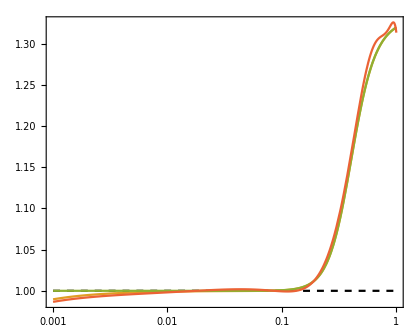

```mathematica
LogLinearPlot[{1,GeffQSASHA2[a]/.k->300H0,Geffstd[a]/.k->300H0,GeffFull[a]/.k->300H0}//Evaluate,{a,ai,1},PlotRange->All,PlotStyle->{Directive[Black,Dashed],"","",""},AspectRatio->0.8,Frame->True,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"a","\\frac{G_\\text{eff}}{G_N}"},RotateLabel->False,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->14},ImageSize->420]
```

### Density Contrast

```mathematica
(* Full expression for the DE contrast using the analytical expressions *)
δFull=1/ρDES(((2 k^2)/((a^)^2)-(F k^2)/((a^)^2)-3 F (H^)^2-3 F Ḣ+72 Subscript[F, R] (H^)^2 Ḣ+18 Subscript[F, R] H^ H^(..)) (^(1)Φ^)+(6 H^-3 F H^-72 Subscript[F, R] H^ Ḣ-18 Subscript[F, R] H^(..)) (^(1)Φ̇)+((F k^2)/((a^)^2)-6 (H^)^2+3 F (H^)^2-3 F Ḣ+216 Subscript[F, R] (H^)^2 Ḣ+54 Subscript[F, R] H^ H^(..)) (^(1)Ψ^)+3 F H^ (^(1)Ψ̇))/.ah[]->a/.H^(..)->HN[Ne]*(HN'[Ne]^2+HN[Ne]*HN''[Ne])/.Ḣ->HN[Ne]*HN'[Ne]/.Hh[]->HN[Ne]/.F->f'[R]/.FR->f''[R]/.R->Ra[Ne]/.Ne->Log[a];
δ1[A_]:=δFull/.(^(1)Φ^)->3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.SolPertsstd/.α->αDES/.k->300H0/.a->A
δ2[A_]:=δFull/.(^(1)Φ^)->3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.SolPertsQSASHA2/.α->αDES/.k->300H0/.a->A
```

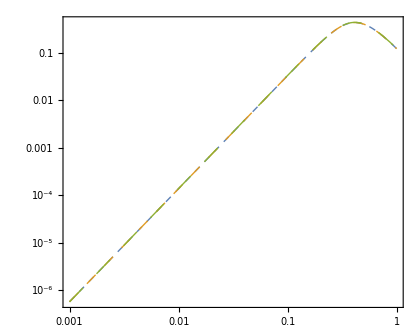

```mathematica
LogLogPlot[{δ2[a],δρQSASHA2[Log[a]]*Ωm[Log[a]]/ΩΛ δm[a]/.SolPertsQSASHA2,δρDEstd[Log[a]]*Ωm[Log[a]]/ΩΛ δm[a]/.SolPertsstd}/.k->300/.α->αDES//Abs//Evaluate,{a,ai,1},PlotRange->All,PlotStyle->{Directive[Dashed,Thick],Directive[Dashing[Medium],Thick],Directive[Dashing[Large],Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["\\delta_\\text{DE}^\\text{Full}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\delta_\\text{DE}^\\text{SHA,2}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\delta_\\text{DE}^\\text{std}"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendMarkerSize->{30,10},LegendFunction->Frame],
{0.18,0.76}],ImageSize->420,AspectRatio->0.8,Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(\\emph{f}DES)}"],Scaled[{0.78,0.25}]]}]
```

### Scalar Velocity

```mathematica
(* Full expression for the DE velocity using the analytical expressions *)
VFull=1/ρDES(((F k^2 H^)/a^-(24 Subscript[F, R] k^2 H^ Ḣ)/a^-(6 Subscript[F, R] k^2 H^(..))/a^) (^(1)Φ^)+(-(2 k^2)/a^+(F k^2)/a^) (^(1)Φ̇)+((2 k^2 H^)/a^-(F k^2 H^)/a^-(48 Subscript[F, R] k^2 H^ Ḣ)/a^-(12 Subscript[F, R] k^2 H^(..))/a^) (^(1)Ψ^)-(F k^2 (^(1)Ψ̇))/a^)/.ah[]->a/.H^(..)->HN[Ne]*(HN'[Ne]^2+HN[Ne]*HN''[Ne])/.Ḣ->HN[Ne]*HN'[Ne]/.Hh[]->HN[Ne]/.F->f'[R]/.FR->f''[R]/.R->Ra[Ne]/.Ne->Log[a];
V1[A_]:=VFull/.(^(1)Φ^)->3Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.SolPertsstd/.α->αDES/.k->300H0/.a->A
V2[A_]:=VFull/.(^(1)Φ^)->3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.SolPertsQSASHA2/.α->αDES/.k->300H0/.a->A
```

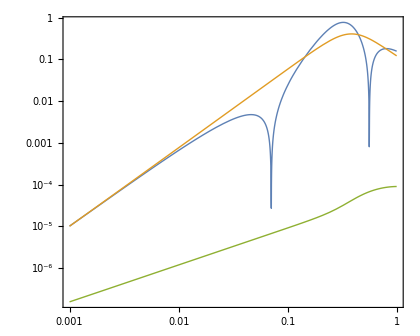

```mathematica
LogLogPlot[{V1[a],VQSASHA2[Log[a]]*Ωm[Log[a]]/ΩΛ δm[a]/.SolPertsQSASHA2,VDEstd[Log[a]]*Ωm[Log[a]]/ΩΛ δm[a]/.SolPertsstd}/.k->300/.α->αDES//Abs//Evaluate,{a,ai,1},PlotRange->All,PlotStyle->{Directive[Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["V_\\text{DE}^\\text{Full}"],
(MaTeX[#,Magnification->1.3]&)/@Style["V_\\text{DE}^\\text{SHA,2}"],
(MaTeX[#,Magnification->1.3]&)/@Style["V_\\text{DE}^\\text{std}"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendMarkerSize->{30,10},LegendFunction->Frame],
{0.18,0.76}],ImageSize->420,AspectRatio->0.8,Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(\\emph{f}DES)}"],Scaled[{0.78,0.18}]]}]
```

### Sound Speed

```mathematica
(* Full expression for the DE Pressure perturbation -> Use it to compute Subscript[c, s]^2 *)
δPFull=(-6 H^+4 F H^) (^(1)Φ̇)+(-2+F) (^(1)Φ^(..))-F (^(1)Ψ^(..))+(^(1)Ψ̇) (2 H^-4 F H^-3 F')+(^(1)Ψ^) (-(2 k^2)/(3 (a^)^2)+6 (H^)^2-3 F (H^)^2+4 Ḣ-3 F Ḣ-6 H^ F'-3 F'')+(^(1)Φ^) (-(2 k^2)/(3 (a^)^2)+3 F (H^)^2+F Ḣ-2 H^ F'-F'')/.ah[]->a/.Ḣ->HN[Ne]*HN'[Ne]/.Hh[]->HN[Ne]/.f->f[R]/.F''->HN[Ne]*HN'[Ne]*FR*Ra'[Ne]+HN[Ne]^2*FR*Ra''[Ne]+HN[Ne]^2*FRR*Ra'[Ne]^2/.F'->HN[Ne]*FR*Ra'[Ne]/.F->f'[R]/.FRR->f'''[R]/.FR->f''[R]/.R->Ra[Ne]/.Ne->Log[a];
δP1[A_]:=δPFull/.(^(1)Φ^)->3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.(^(1)Φ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a],a]/.(^(1)Ψ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a],a]/.SolPertsstd/.α->αDES/.k->300H0/.a->A
δP2[A_]:=δPFull/.(^(1)Φ^)->3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.(^(1)Φ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a],a]/.(^(1)Ψ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a],a]/.SolPertsQSASHA2/.α->αDES/.k->300H0/.a->A
```

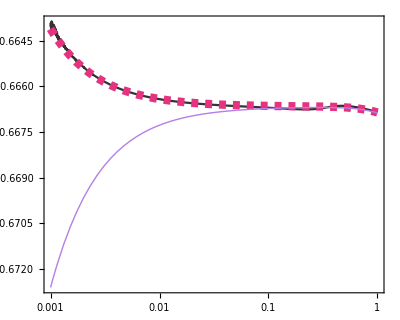

```mathematica
LogLinearPlot[{δP2[a]/(ρDES*δ2[a]),cs2QSASHA2[Log[a]],δPDEstd[Log[a]]/δρDEstd[Log[a]]}/.k->300/.α->αDES//Evaluate,{a,ai,1},PlotRange->All,PlotStyle->{Directive[Black,Opacity[0.8]],Directive[Thickness[0.015],Dashed,RGBColor[0.9,0.2,0.5]],Directive[Thick,RGBColor[0.7,0.5,0.9]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["c_{s, \\text{Full}}^2"],
(MaTeX[#,Magnification->1.3]&)/@Style["c_{s, \\text{SHA}}^2"],
(MaTeX[#,Magnification->1.3]&)/@Style["c_{s, \\text{std}}^2"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendMarkerSize->{30,10},LegendFunction->Frame],
{0.82,0.25}],ImageSize->400,AspectRatio->0.8,Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(\\emph{f}DES)}"],Scaled[{0.78,0.83}]]}]
```

### Effective Sound Speed

```mathematica
πFull=k^2/a^2*(FR*δR-(1-F)((^(1)Φ^)+(^(1)Ψ^)))/.δR->(4 k^2 (^(1)Φ^))/((a^)^2)+24 H^ (^(1)Φ̇)+6 (^(1)Φ^(..))+(2 k^2 (^(1)Ψ^))/((a^)^2)-24 (H^)^2 (^(1)Ψ^)-12 Ḣ (^(1)Ψ^)-6 H^ (^(1)Ψ̇)/.ah[]->a/.Ḣ->HN[Ne]*HN'[Ne]/.Hh[]->HN[Ne]/.f->f[R]/.F''->HN[Ne]*HN'[Ne]*FR*Ra'[Ne]+HN[Ne]^2*FR*Ra''[Ne]+HN[Ne]^2*FRR*Ra'[Ne]^2/.F'->HN[Ne]*FR*Ra'[Ne]/.F->f'[R]/.FRR->f'''[R]/.FR->f''[R]/.R->Ra[Ne]/.Ne->Log[a];
π1[A_]:=πFull/.(^(1)Φ^)->3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.(^(1)Φ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a],a]/.(^(1)Ψ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a],a]/.SolPertsstd/.α->αDES/.k->300H0/.a->A
π2[A_]:=πFull/.(^(1)Φ^)->3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.(^(1)Φ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a],a]/.(^(1)Ψ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a],a]/.SolPertsQSASHA2/.α->αDES/.k->300H0/.a->A
```

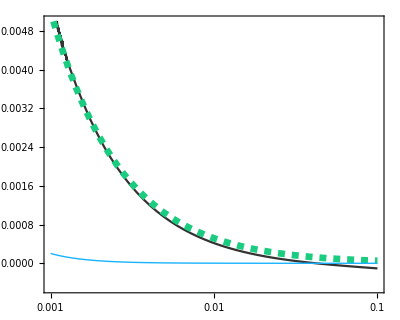

```mathematica
LogLinearPlot[{δP2[a]/(ρDES*δ2[a])-2/3*π2[a]/(ρDES*δ2[a]),cs2effQSASHA2[Log[a]],δPDEstd[Log[a]]/δρDEstd[Log[a]]-2/3*πDEstd[Log[a]]/δρDEstd[Log[a]]}/.k->300/.α->αDES//Evaluate,{a,ai,0.1},PlotRange->{-0.0005,0.005},PlotStyle->{Directive[Black,Opacity[0.8]],Directive[Thickness[0.012],Dashed,RGBColor[0.1,0.8,0.5]],Directive[Thick,RGBColor[0.1,0.7,1]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["c_{\\text{eff}, \\text{Full}}^2"],
(MaTeX[#,Magnification->1.3]&)/@Style["c_{\\text{eff}, \\text{SHA}}^2"],
(MaTeX[#,Magnification->1.3]&)/@Style["c_{\\text{eff}, \\text{std}}^2"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendMarkerSize->{30,10},LegendFunction->Frame],
{0.81,0.75}],ImageSize->400,AspectRatio->0.8,Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(\\emph{f}DES)}"],Scaled[{0.81,0.35}]]}]
```

## CMB Angular and Matter Power Spectra

```mathematica
Off[Import::"noelem"]
```

```mathematica
dataPk1=Import["/Users/cosmologygroup/CLASS/EFCLASS/output/fDES00_pk.dat",{"Data",{All},{1,2}}];
dataPk2=Import["/Users/cosmologygroup/CLASS/EFCLASS/output/fDES01_pk.dat",{"Data",{All},{1,2}}];
dataPkΛCDM=Import["/Users/cosmologygroup/CLASS/EFCLASS/output/base_2018_plikHM_TTTEEE_lowl_lowE_lensing00_pk.dat",{"Data",{All},{1,2}}];
```

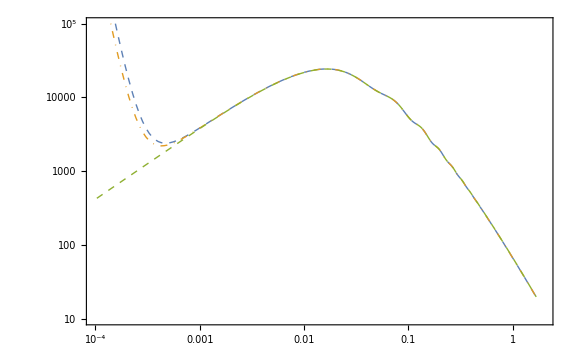

```mathematica
MatterSpectrum=ListLogLogPlot[{dataPk1,dataPk2,dataPkΛCDM},PlotRange->{{10^-4,2},{10,10^5}},Joined->True,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"k \\left[ h \\text{Mpc}^{-1} \\right]","P(k) \\left[ (h^{-1} \\text{Mpc})^3 \\right]"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotStyle->{Directive[Thick,Dashed],Directive[Thick,DotDashed],Directive[Thick,Dashed]},PlotLegends->Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["\\text{Standard QSA-SHA}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\text{New QSA-SHA}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\Lambda\\text{CDM}"]},
LegendLayout->{"Row",4},LabelStyle->{Black,Bold,5},LegendFunction->Frame],
{0.5,0.25}],Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(\\emph{f}DES)}"],Scaled[{0.85,0.82}]]}]
```

```mathematica
dataClTT1=Import["/Users/cosmologygroup/CLASS/EFCLASS/output/fDES00_cl.dat",{"Data",{All},{1,2}}];
dataClTT2=Import["/Users/cosmologygroup/CLASS/EFCLASS/output/fDES01_cl.dat",{"Data",{All},{1,2}}];
dataClTTΛCDM=Import["/Users/cosmologygroup/CLASS/EFCLASS/output/base_2018_plikHM_TTTEEE_lowl_lowE_lensing00_cl.dat",{"Data",{All},{1,2}}];
```

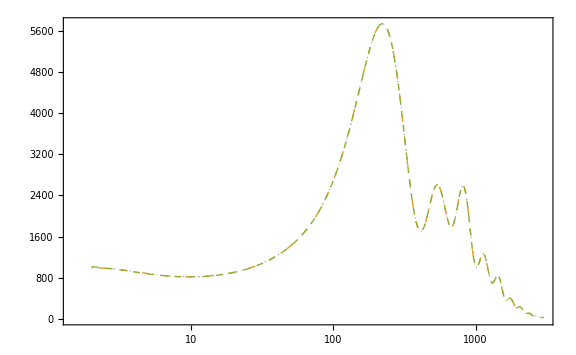

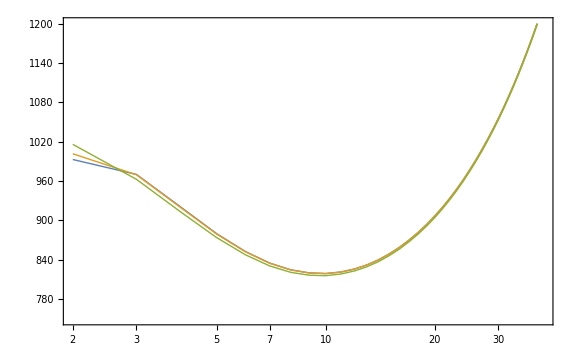

```mathematica
(* This is necessary in order to get the right units. *)
ClTT1={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClTT1; 
ClTT2={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClTT2; 
ClTTΛCDM={#[[1]],Abs[#[[2]]*(2.7255*10^6)^2]}&/@dataClTTΛCDM;
TTSpectrum=ListLogLinearPlot[{ClTT1,ClTT2,ClTTΛCDM},Joined->True,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"l","l(l + 1)C_l^{TT} \\left[ \\mu \\text{K}^2 \\right]"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Directive[Thick,Dotted],Directive[Thick,DotDashed],Directive[Thick,Dashed],Directive[Thick,Dashing[Large]]},PlotLegends->Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Standard QSA-SHA}"],
(MaTeX[#,Magnification->1.2]&)/@Style["\\text{New QSA-SHA}"],
(MaTeX[#,Magnification->1.2]&)/@Style["\\Lambda\\text{CDM}"]},
LegendLayout->{"Row",4},LabelStyle->{Black,Bold,5},LegendFunction->Frame],
{0.23,0.8}],ImageSize->Large]
TTSpectrum=ListLogLinearPlot[{ClTT1,ClTT2,ClTTΛCDM},PlotRange->{{2,40},{750,1200}},Joined->True,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"l","l(l + 1)C_l^{TT} \\left[ \\mu \\text{K}^2 \\right]"},BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->{Directive[Thick],Directive[Thick]},PlotLegends->Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\text{Standard QSA-SHA}"],
(MaTeX[#,Magnification->1.2]&)/@Style["\\text{New QSA-SHA}"],
(MaTeX[#,Magnification->1.2]&)/@Style["\\Lambda\\text{CDM}"]},
LegendLayout->{"Row",4},LabelStyle->{Black,Bold,5},LegendFunction->Frame],
{0.5,0.7}],ImageSize->Large]
```

## Full Solution: k=100 H_0

### QSA-SHA Solutions

#### Standard Procedure

```mathematica
Φstd[Ne_]:=(2 Subscript[F, R] k^2 (a^)^2+F (a^)^4)/(6 F Subscript[F, R] k^4+2 F^2 k^2 (a^)^2)/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
Ψstd[Ne_]:=-(4 Subscript[F, R] k^2 (a^)^2+F (a^)^4)/(6 F Subscript[F, R] k^4+2 F^2 k^2 (a^)^2)/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
δρDEstd[Ne_]:=-((-2+3 F) Subscript[F, R] k^2+(-1+F) F (a^)^2)/(F (3 Subscript[F, R] k^2+F (a^)^2))/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
δPDEstd[Ne_]:=(2 Subscript[F, R] k^4+15 Subscript[F, R] k^2 (a^)^2 F''+3 F (a^)^4 F'')/(9 F Subscript[F, R] k^4+3 F^2 k^2 (a^)^2)/.ah[]->aN[Ne]/.F''->HN[Ne]*HN'[Ne]*FR*Ra'[Ne]+HN[Ne]^2*FR*Ra''[Ne]+HN[Ne]^2*FRR*Ra'[Ne]^2/.F->f'[R]/.FRR->f'''[R]/.FR->f''[R]/.R->Ra[Ne]
VDEstd[Ne_]:=(a^ (6 Subscript[F, R] k^2+F (a^)^2) F')/(2 F (3 Subscript[F, R] k^2+F (a^)^2))/.ah[]->aN[Ne]/.F'->HN[Ne]*FR*Ra'[Ne]/.F->f'[R]/.FR->f''[R]/.R->Ra[Ne]
πDEstd[Ne_]:=1/F*(k^2/a^2*FR/F)/(1+3 k^2/a^2*FR/F)/.a->aN[Ne]/.F->f'[R]/.FR->f''[R]/.R->Ra[Ne]
```

```mathematica
(* Initial conditions *)
δ0=1; (* Overall Scale *)
ai=10^-3;(* Initial scale factor *)
δmi=δ0*ai(1+3*(HN[Log[ai]]^2*ai^2)/k^2);
Vmi=-δ0*H0*√Ωm0*ai^(1/2);
Φistd=Φstd[Log[a]]*3 H0^2 Ωm[Log[a]]*δmi/.α->αDES/.k->100/.a->ai//Quiet;
Ψistd=Ψstd[Log[a]]*3 H0^2 Ωm[Log[a]]*δmi/.α->αDES/.k->100/.a->ai//Quiet;

(* Evolution Equations Matter *)
Eqδm[a_]:=-δm'[a]-Vm[a]/(a^2*HN[Log[a]])-3D[Φstd[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a],a];
EqVm[a_]:=-Vm'[a]-Vm[a]/a+k^2/(a^2*HN[Log[a]])Ψstd[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a];
```

```mathematica
SolPertsstd=NDSolve[{Eqδm[a]==0,EqVm[a]==0,
δm[ai]==δmi,Vm[ai]==Vmi}/.α->αDES/.k->100H0,{δm,Vm},{a,ai,1},MaxStepSize->10^-4,MaxStepFraction->10^-4,StartingStepSize->10^-4,PrecisionGoal->11,AccuracyGoal->11,MaxSteps->20000000,InterpolationOrder->All,Method->{"EquationSimplification"->"Residual"}][[1]];
```

#### 2^nd Order in SHA

```mathematica
(* Don't forget the factors Subscript[ρ̄, m] Subscript[δ, m] for the potentials and Subscript[ρ̄, m]/Subscript[ρ̄, DE] Subscript[δ, m] for the other perturbations *)
ΦQSASHA2[Ne_]:=(2 Subscript[F, R] k^2 (a^)^2+F (a^)^4)/(6 F Subscript[F, R] k^4+2 F^2 k^2 (a^)^2)-(3 ((a^)^2 (F^2 (a^)^4+F Subscript[F, R] k^2 (a^)^2 (8+δ)+2 Subscript[F, R]^2 k^4 (8+3 δ))) ε^2)/(2 (F (3 Subscript[F, R] k^3+F k (a^)^2)^2))/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
ΨQSASHA2[Ne_]:=-(4 Subscript[F, R] k^2 (a^)^2+F (a^)^4)/(6 F Subscript[F, R] k^4+2 F^2 k^2 (a^)^2)+(3 (a^)^2 (4 Subscript[F, R] k^2+F (a^)^2) (F (a^)^2+Subscript[F, R] k^2 (2-3 δ)) ε^2)/(2 F (3 Subscript[F, R] k^3+F k (a^)^2)^2)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
δρQSASHA2[Ne_]:=((2-3 F) Subscript[F, R] k^2-(-1+F) F (a^)^2)/(F (3 Subscript[F, R] k^2+F (a^)^2))-(3 (Subscript[F, R] k^2 (F (a^)^2 (1+δ)+2 Subscript[F, R] k^2 (2+3 δ))) ε^2)/(F (3 Subscript[F, R] k^2+F (a^)^2)^2)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
δPQSASHA2[Ne_]:=(2 Subscript[F, R] k^2)/(9 F Subscript[F, R] k^2+3 F^2 (a^)^2)+(((-1+F) F^2 (a^)^4 (1+2 δ)+F Subscript[F, R] k^2 (a^)^2 (-5+5 F-10 δ+13 F δ)+Subscript[F, R]^2 k^4 (-4-6 δ+3 F (2+7 δ))) ε^2)/(F (3 Subscript[F, R] k^2+F (a^)^2)^2)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
VQSASHA2[Ne_]:=(((-4+3 F) Subscript[F, R] k^3+(-1+F) F k (a^)^2) ε)/(F (3 Subscript[F, R] k^2+F (a^)^2))/.ε->εSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
πQSASHA2[Ne_]:=(Subscript[F, R] k^2)/(3 F Subscript[F, R] k^2+F^2 (a^)^2)+(3 Subscript[F, R] k^2 (Subscript[F, R] k^2 (4+9 δ)+(F+2 F δ) (a^)^2) ε^2)/(F (3 Subscript[F, R] k^2+F (a^)^2)^2)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]
cs2QSASHA2[Ne_]:=-(2 (Subscript[F, R] k^2))/(3 (-2+3 F) Subscript[F, R] k^2+3 (-1+F) F (a^)^2)-(F ((-1+F)^2 F (a^)^4 (1+2 δ)+Subscript[F, R]^2 k^4 (-8+6 F-20 δ+21 F δ)+(-1+F) Subscript[F, R] k^2 (a^)^2 (-4-8 δ+F (5+13 δ))) ε^2)/(((-2+3 F) Subscript[F, R] k^2+(-1+F) F (a^)^2)^2)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.α->αDES
cs2effQSASHA2[Ne_]:=((-((-1+F) F (a^)^2 (1+2 δ))+Subscript[F, R] k^2 (4+8 δ-F (2+7 δ))) ε^2)/((-2+3 F) Subscript[F, R] k^2+(-1+F) F (a^)^2)/.ε->εSHA[Ne,k]/.δ->δSHA[Ne,k]/.ah[]->aN[Ne]/.FR->f''[R]/.F->f'[R]/.R->Ra[Ne]/.α->αDES
```

```mathematica
(* Initial conditions *)
δ0=1; (* Overall Scale *)
ai=10^-3;(* Initial scale factor *)
δmi=δ0*ai(1+3*(HN[Log[ai]]^2*ai^2)/k^2);
Vmi=-δ0*H0*√Ωm0*ai^(1/2);
ΦiQSASHA=ΦQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δmi/.α->αDES/.k->100/.a->ai//Quiet;
ΨiQSASHA=ΨQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δmi/.α->αDES/.k->100/.a->ai//Quiet;
(* Evolution Equations Matter *)
Eqδm[a_]:=-δm'[a]-Vm[a]/(a^2*HN[Log[a]])-3D[ΦQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a],a];
EqVm[a_]:=-Vm'[a]-Vm[a]/a+k^2/(a^2*HN[Log[a]])ΨQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a];
```

```mathematica
SolPertsQSASHA2=NDSolve[{Eqδm[a]==0,EqVm[a]==0,
δm[ai]==δmi,Vm[ai]==Vmi}/.α->αDES/.k->100H0,{δm,Vm},{a,ai,1},Method->{"EquationSimplification"->"Residual"}][[1]];
```

### Fortran Data

```mathematica
DataFortran=Import["/Users/cosmologygroup/Desktop/QSA_Project/Theoretical_Work/Bayron/fDES_k_100.txt","Data"];
DataΔ=DataFortran[[All,{1,2}]];
Datav=DataFortran[[All,{1,3}]];
DataΦPlus=DataFortran[[All,{1,4}]];
Dataχ=DataFortran[[All,{1,5}]];
```

```mathematica
DataΦ=Table[{DataΦPlus[[i,1]],(-DataΦPlus[[i,2]]-Dataχ[[i,2]]/(2F))}/.F->f'[R]/.R->Ra[Ne]/.Ne->Log[DataΦPlus[[i,1]]]/.α->αDES//N,{i,1,Length[DataΦPlus]}];
DataΨ=Table[{DataΦPlus[[i,1]],(DataΦPlus[[i,2]]-Dataχ[[i,2]]/(2F))}/.F->f'[R]/.R->Ra[Ne]/.Ne->Log[DataΦPlus[[i,1]]]/.α->αDES//N,{i,1,Length[DataΦPlus]}];
```

### Potentials

```mathematica
ΦSR[a_]=ΦiQSASHA*FindFormula[DataΦ][a]//Expand
ΨSR[a_]=-ΨiQSASHA*FindFormula[DataΨ][a]//Expand
```

0.0000463285-0.0000104409 a+0.0000995035 a^2-0.000357972 a^3+0.000377803 a^4-0.00012858 a^5

-0.0000458441-9.89669×10^-6 a+0.0000931095 a^2-0.00029139 a^3+0.000318635 a^4-0.000112365 a^5

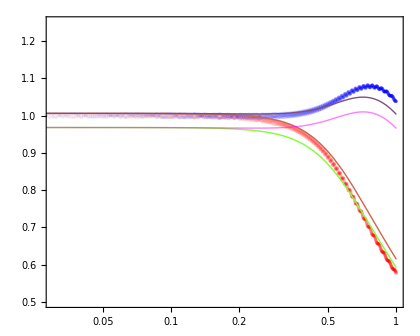

```mathematica
(* Comparison of the Potentials *)
ListLogLinearPlot[{DataΦ,DataΨ}//Abs,PlotRange->All,PlotStyle->{Directive[PointSize[0.006],Red,Opacity[0.1]],Directive[PointSize[0.006],Blue,Opacity[0.1]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},RotateLabel->False,BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["\\Phi^\\text{Full}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\Psi^\\text{Full}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,30},LegendMarkerSize->{25,25}],
{0.32,0.38}],ImageSize->420,AspectRatio->0.8];
LogLinearPlot[{(ΦQSASHA2[Log[a]]*3 H0^2*Ωm[Log[a]]*δm[a])/(ΦQSASHA2[Log[ai]]*3 H0^2*Ωm[Log[ai]]*δm[ai])/.SolPertsQSASHA2,(Φstd[Log[a]]*3 H0^2*Ωm[Log[a]]*δm[a])/(Φstd[Log[ai]]*3 H0^2*Ωm[Log[ai]]*δm[ai])/.SolPertsstd,(ΨQSASHA2[Log[a]]*3 H0^2*Ωm[Log[a]]*δm[a])/(ΨQSASHA2[Log[ai]]*3 H0^2*Ωm[Log[ai]]*δm[ai])/.SolPertsQSASHA2,(Ψstd[Log[a]]*3 H0^2*Ωm[Log[a]]*δm[a])/(Ψstd[Log[ai]]*3 H0^2*Ωm[Log[ai]]*δm[ai])/.SolPertsstd}/.α->αDES/.k->100H0//Abs//Evaluate,{a,ai,1},PlotRange->All,PlotStyle->{Directive[RGBColor[0.8,0.4,0.3],Thick],Directive[Thick,RGBColor[0.5,1,0.2]],Directive[RGBColor[0.5,0.3,0.5],Thick],Directive[Thick,Magenta,Opacity[0.5]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},RotateLabel->False,BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["\\Phi^\\text{SHA, 2}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\Phi^\\text{std}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\Psi^\\text{SHA, 2}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\Psi^\\text{std}"]},
LegendLayout->{"Row",2},LabelStyle->{Black,Bold,10},LegendMarkerSize->{35,15}],
{0.3,0.18}],ImageSize->420,AspectRatio->0.8];
Show[%%,%,PlotRange->{{Log[0.03],Log[1]},{0.5,1.25}},Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["k = 100 H_0"],Scaled[{0.2,0.82}]]}]
```

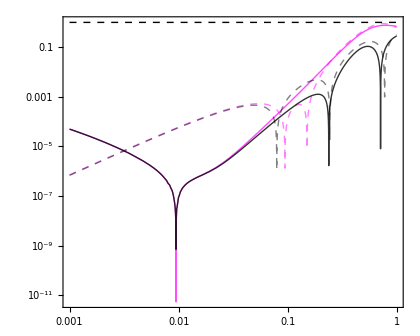

```mathematica
(* Comparison of the several ε parameters  *)
LogLogPlot[{D[ΦQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a],a]/(ΦQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a]*a*HN[Log[a]]^2)/.SolPertsQSASHA2,ΦSR'[a]/(ΦSR[a]*a*HN[Log[a]]^2),D[ΨQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a],a]/(ΨQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a]*a*HN[Log[a]]^2)/.SolPertsQSASHA2,ΨSR'[a]/(ΨSR[a]*a*HN[Log[a]]^2),1}/.α->αDES/.k->100H0//Abs//Evaluate,{a,ai,1},PlotRange->All,PlotStyle->{Directive[Thick,Magenta,Opacity[0.7]],Directive[Thick,Dashed,Magenta,Opacity[0.5]],Directive[Thick,Black,Opacity[0.8]],Directive[Thick,Black,Opacity[0.5],Dashed],Directive[Thick,Black,Dashed]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["\\varepsilon_\\Phi^\\text{SHA, 2}"],(MaTeX[#,Magnification->1.3]&)/@Style["\\varepsilon_\\Phi^\\text{Full}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\varepsilon_\\Psi^\\text{SHA, 2}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\varepsilon_\\Psi^\\text{Full}"]},
LegendLayout->{"Row",2},LabelStyle->{Black,Bold,15},LegendMarkerSize->{30,10},LegendFunction->Frame],
{0.72,0.19}],ImageSize->420,AspectRatio->0.8,Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(\\emph{f}DES)}"],Scaled[{0.2,0.8}]]}]
```

```mathematica
(* Values of Subscript[ε, Φ] and Subscript[ε, Ψ] today *)
D[ΨQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a],a]/(ΨQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a]*a*HN[Log[a]]^2)/.k->100H0/.α->αDES/.SolPertsQSASHA2/.a->1
D[ΦQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a],a]/(ΦQSASHA2[Log[a]]*3 H0^2 Ωm[Log[a]]*δm[a]*a*HN[Log[a]]^2)/.k->100H0/.α->αDES/.SolPertsQSASHA2/.a->1
```

-0.282065

-0.690224

### Density Contrast

```mathematica
(* Full expression for the DE contrast using the analytical expressions *)
δFull=1/ρDES(((2 k^2)/((a^)^2)-(F k^2)/((a^)^2)-3 F (H^)^2-3 F Ḣ+72 Subscript[F, R] (H^)^2 Ḣ+18 Subscript[F, R] H^ H^(..)) (^(1)Φ^)+(6 H^-3 F H^-72 Subscript[F, R] H^ Ḣ-18 Subscript[F, R] H^(..)) (^(1)Φ̇)+((F k^2)/((a^)^2)-6 (H^)^2+3 F (H^)^2-3 F Ḣ+216 Subscript[F, R] (H^)^2 Ḣ+54 Subscript[F, R] H^ H^(..)) (^(1)Ψ^)+3 F H^ (^(1)Ψ̇))/.ah[]->a/.H^(..)->HN[Ne]*(HN'[Ne]^2+HN[Ne]*HN''[Ne])/.Ḣ->HN[Ne]*HN'[Ne]/.Hh[]->HN[Ne]/.F->f'[R]/.FR->f''[R]/.R->Ra[Ne]/.Ne->Log[a];
δ1[A_]:=δFull/.(^(1)Φ^)->3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.SolPertsstd/.α->αDES/.k->100H0/.a->A
δ2[A_]:=δFull/.(^(1)Φ^)->3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.SolPertsQSASHA2/.α->αDES/.k->100H0/.a->A
```

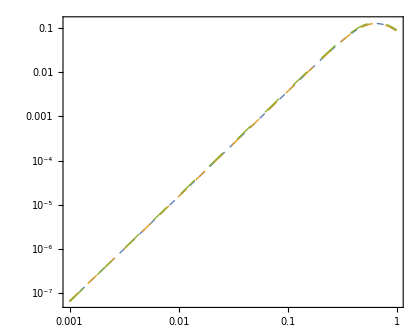

```mathematica
LogLogPlot[{δ2[a],δρQSASHA2[Log[a]]*Ωm[Log[a]]/ΩΛ δm[a]/.SolPertsQSASHA2,δρDEstd[Log[a]]*Ωm[Log[a]]/ΩΛ δm[a]/.SolPertsstd}/.k->100/.α->αDES//Abs//Evaluate,{a,ai,1},PlotRange->All,PlotStyle->{Directive[Dashed,Thick],Directive[Dashing[Medium],Thick],Directive[Dashing[Large],Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["\\delta_\\text{DE}^\\text{Full}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\delta_\\text{DE}^\\text{SHA,2}"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\delta_\\text{DE}^\\text{std}"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendMarkerSize->{30,10},LegendFunction->Frame],
{0.18,0.76}],ImageSize->420,AspectRatio->0.8,Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(\\emph{f}DES)}"],Scaled[{0.78,0.25}]]}]
```

### Scalar Velocity

```mathematica
(* Full expression for the DE velocity using the analytical expressions *)
VFull=1/ρDES(((F k^2 H^)/a^-(24 Subscript[F, R] k^2 H^ Ḣ)/a^-(6 Subscript[F, R] k^2 H^(..))/a^) (^(1)Φ^)+(-(2 k^2)/a^+(F k^2)/a^) (^(1)Φ̇)+((2 k^2 H^)/a^-(F k^2 H^)/a^-(48 Subscript[F, R] k^2 H^ Ḣ)/a^-(12 Subscript[F, R] k^2 H^(..))/a^) (^(1)Ψ^)-(F k^2 (^(1)Ψ̇))/a^)/.ah[]->a/.H^(..)->HN[Ne]*(HN'[Ne]^2+HN[Ne]*HN''[Ne])/.Ḣ->HN[Ne]*HN'[Ne]/.Hh[]->HN[Ne]/.F->f'[R]/.FR->f''[R]/.R->Ra[Ne]/.Ne->Log[a];
V1[A_]:=VFull/.(^(1)Φ^)->3Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.SolPertsstd/.α->αDES/.k->100H0/.a->A
V2[A_]:=VFull/.(^(1)Φ^)->3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.SolPertsQSASHA2/.α->αDES/.k->100H0/.a->A
```

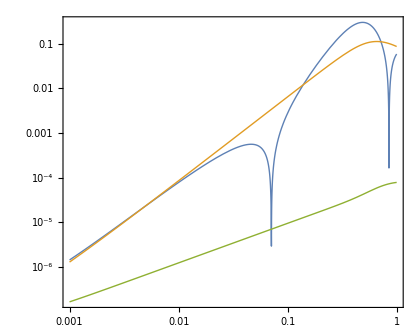

```mathematica
LogLogPlot[{V1[a],VQSASHA2[Log[a]]*Ωm[Log[a]]/ΩΛ δm[a]/.SolPertsQSASHA2,VDEstd[Log[a]]*Ωm[Log[a]]/ΩΛ δm[a]/.SolPertsstd}/.k->100H0/.α->αDES//Abs//Evaluate,{a,ai,1},PlotRange->All,PlotStyle->{Directive[Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["V_\\text{DE}^\\text{Full}"],
(MaTeX[#,Magnification->1.3]&)/@Style["V_\\text{DE}^\\text{SHA,2}"],
(MaTeX[#,Magnification->1.3]&)/@Style["V_\\text{DE}^\\text{std}"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendMarkerSize->{30,10},LegendFunction->Frame],
{0.18,0.76}],ImageSize->420,AspectRatio->0.8,Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(\\emph{f}DES)}"],Scaled[{0.78,0.18}]]}]
```

### Sound Speed

```mathematica
(* Full expression for the DE Pressure perturbation -> Use it to compute Subscript[c, s]^2 *)
δPFull=(-6 H^+4 F H^) (^(1)Φ̇)+(-2+F) (^(1)Φ^(..))-F (^(1)Ψ^(..))+(^(1)Ψ̇) (2 H^-4 F H^-3 F')+(^(1)Ψ^) (-(2 k^2)/(3 (a^)^2)+6 (H^)^2-3 F (H^)^2+4 Ḣ-3 F Ḣ-6 H^ F'-3 F'')+(^(1)Φ^) (-(2 k^2)/(3 (a^)^2)+3 F (H^)^2+F Ḣ-2 H^ F'-F'')/.ah[]->a/.Ḣ->HN[Ne]*HN'[Ne]/.Hh[]->HN[Ne]/.f->f[R]/.F''->HN[Ne]*HN'[Ne]*FR*Ra'[Ne]+HN[Ne]^2*FR*Ra''[Ne]+HN[Ne]^2*FRR*Ra'[Ne]^2/.F'->HN[Ne]*FR*Ra'[Ne]/.F->f'[R]/.FRR->f'''[R]/.FR->f''[R]/.R->Ra[Ne]/.Ne->Log[a];
δP1[A_]:=δPFull/.(^(1)Φ^)->3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.(^(1)Φ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a],a]/.(^(1)Ψ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a],a]/.SolPertsstd/.α->αDES/.k->100H0/.a->A
δP2[A_]:=δPFull/.(^(1)Φ^)->3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.(^(1)Φ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a],a]/.(^(1)Ψ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a],a]/.SolPertsQSASHA2/.α->αDES/.k->100H0/.a->A
```

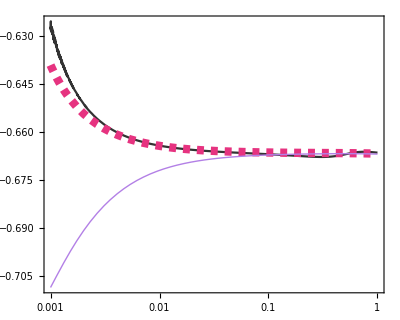

```mathematica
LogLinearPlot[{δP2[a]/(ρDES*δ2[a]),cs2QSASHA2[Log[a]],δPDEstd[Log[a]]/δρDEstd[Log[a]]}/.k->100H0/.α->αDES//Evaluate,{a,ai,1},PlotRange->All,PlotStyle->{Directive[Black,Opacity[0.8]],Directive[Thickness[0.015],Dashed,RGBColor[0.9,0.2,0.5]],Directive[Thick,RGBColor[0.7,0.5,0.9]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["c_{s, \\text{Full}}^2"],
(MaTeX[#,Magnification->1.3]&)/@Style["c_{s, \\text{SHA}}^2"],
(MaTeX[#,Magnification->1.3]&)/@Style["c_{s, \\text{std}}^2"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendMarkerSize->{30,10},LegendFunction->Frame],
{0.82,0.25}],ImageSize->400,AspectRatio->0.8,Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(\\emph{f}DES)}"],Scaled[{0.78,0.83}]]}]
```

### Effective Sound Speed

```mathematica
πFull=k^2/a^2*(FR*δR-(1-F)((^(1)Φ^)+(^(1)Ψ^)))/.δR->(4 k^2 (^(1)Φ^))/((a^)^2)+24 H^ (^(1)Φ̇)+6 (^(1)Φ^(..))+(2 k^2 (^(1)Ψ^))/((a^)^2)-24 (H^)^2 (^(1)Ψ^)-12 Ḣ (^(1)Ψ^)-6 H^ (^(1)Ψ̇)/.ah[]->a/.Ḣ->HN[Ne]*HN'[Ne]/.Hh[]->HN[Ne]/.f->f[R]/.F''->HN[Ne]*HN'[Ne]*FR*Ra'[Ne]+HN[Ne]^2*FR*Ra''[Ne]+HN[Ne]^2*FRR*Ra'[Ne]^2/.F'->HN[Ne]*FR*Ra'[Ne]/.F->f'[R]/.FRR->f'''[R]/.FR->f''[R]/.R->Ra[Ne]/.Ne->Log[a];
π1[A_]:=πFull/.(^(1)Φ^)->3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a]/.(^(1)Φ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*Φstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a],a]/.(^(1)Ψ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*Ψstd[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsstd,a],a]/.SolPertsstd/.α->αDES/.k->100H0/.a->A
π2[A_]:=πFull/.(^(1)Φ^)->3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Ψ^)->3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.(^(1)Φ̇)->1/(a*HN[Log[a]])D[3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.(^(1)Ψ̇)->1/(a*HN[Log[a]])D[3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a]/.(^(1)Φ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*ΦQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a],a]/.(^(1)Ψ^(..))->1/(a*HN[Log[a]])D[1/(a*HN[Log[a]])D[3*ΨQSASHA2[Log[a]]*Ωm[Log[a]]*δm[a]/.SolPertsQSASHA2,a],a]/.SolPertsQSASHA2/.α->αDES/.k->100H0/.a->A
```

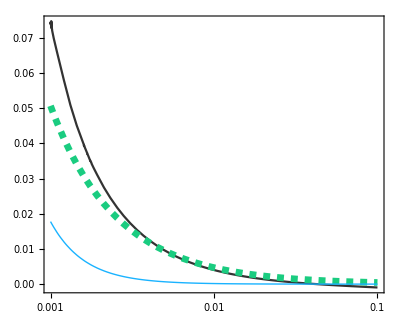

```mathematica
LogLinearPlot[{δP2[a]/(ρDES*δ2[a])-2/3*π2[a]/(ρDES*δ2[a]),cs2effQSASHA2[Log[a]],δPDEstd[Log[a]]/δρDEstd[Log[a]]-2/3*πDEstd[Log[a]]/δρDEstd[Log[a]]}/.k->100H0/.α->αDES//Evaluate,{a,ai,0.1},PlotRange->All,PlotStyle->{Directive[Black,Opacity[0.8]],Directive[Thickness[0.012],Dashed,RGBColor[0.1,0.8,0.5]],Directive[Thick,RGBColor[0.1,0.7,1]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.6]&)/@{"a"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.3]&)/@Style["c_{\\text{eff}, \\text{Full}}^2"],
(MaTeX[#,Magnification->1.3]&)/@Style["c_{\\text{eff}, \\text{SHA}}^2"],
(MaTeX[#,Magnification->1.3]&)/@Style["c_{\\text{eff}, \\text{std}}^2"]},
LegendLayout->{"Row",3},LabelStyle->{Black,Bold,15},LegendMarkerSize->{30,10},LegendFunction->Frame],
{0.81,0.75}],ImageSize->400,AspectRatio->0.8,Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\textbf{(\\emph{f}DES)}"],Scaled[{0.81,0.35}]]}]
```